# Max of coherent information - computations

This notebook is to be used to compute the maximum coherent information of the finite dimensional MAD channels (which are the qudit extensions of ADC’s)

QuantumUtils is needed for this notebook. A function to easily add assumptions to $Assumptions is defined.

```mathematica
Needs["QuantumUtils`"]
Needs["MaTeX`"]
AddAssumption[assumption_]:=$Assumptions=DeleteDuplicates[$Assumptions&&assumption];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color}"}];
```

AssignUsage::nousg: No usage message in UsageData[] for symbol PossiblyTrueQ found; using a blank message instead.

AssignUsage::nousg: No usage message in UsageData[] for symbol PossiblyFalseQ found; using a blank message instead.

AssignUsage::nousg: No usage message in UsageData[] for symbol PossiblyNonzeroQ found; using a blank message instead.

General::stop: Further output of AssignUsage::nousg will be suppressed during this calculation.

Needs package to export cells to TEX

```mathematica
Needs["CellsToTeX`"]
```

GatherBy::list: List expected at position 1 in GatherBy[System`ConvertersDump`$extensionMappings,Last].

Part::partd: Part specification GatherBy[System`ConvertersDump`$extensionMappings,Last]⟦All,1⟧ is longer than depth of object.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[System`ConvertersDump`$extensionMappings,1].

First::normal: Nonatomic expression expected at position 1 in First[All].

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[First[All],1].

Last::normal: Nonatomic expression expected at position 1 in Last[All].

First::normal: Nonatomic expression expected at position 1 in First[1].

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[First[1],1].

General::stop: Further output of StringDrop::strse will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[1].

## Setting

### Dimension

Set the dimension of the Hilbert Space

```mathematica
d=4;
```

### Input state

Use this function to generate a d-dimensional generic density matrix

```mathematica
BuildDensityStandard[par_]:=(
ρSys=ConstantArray[0,{d,d}];
Do[
ρSys[[i1,j1]]=ToExpression[ToString[par]<>ToString[i1-1]<>ToString[j1-1]];
ρSys[[j1,i1]]=Conjugate[ToExpression[ToString[par]<>ToString[i1-1]<>ToString[j1-1]]],
{j1,1,d},{i1,1,j1-1}
];
Do[
AddAssumption[Element[ToExpression[ToString[par]<>ToString[j1-1]<>ToString[j1-1]],Reals]];
AddAssumption[0<=ToExpression[ToString[par]<>ToString[j1-1]<>ToString[j1-1]]<=1];
ρSys[[j1,j1]]=ToExpression[ToString[par]<>ToString[j1-1]<>ToString[j1-1]],
{j1,1,d}
];
(*AddAssumption[Sum[ToExpression[ToString[par]<>ToString[j-1]<>ToString[j-1]],{j,1,d}]==1];*)
ρSys//Simplify
)
ρA//Clear
ρA=BuildDensityStandard[ρ];
```

Create density matrix for TEX exports

```mathematica
BuildDensityTeX[par_]:=(
protected=Unprotect[Conjugate];
ρSys = ConstantArray[0,{d,d}];

Do[
ρSys[[i1,j1]]=Subscript[par,ToString[i1-1]<>ToString[j1-1]];
ρSys[[j1,i1]]=Conjugate[Subscript[par,ToString[i1-1]<>ToString[j1-1]]],
{j1,1,d},{i1,1,j1-1}
];
Do[
Conjugate[Subscript[par,ToString[j1-1]<>ToString[j1-1]]]=Subscript[par,ToString[j1-1]<>ToString[j1-1]];
Part[ρSys,j1,j1]=Subscript[par,ToString[j1-1]<>ToString[j1-1]],
{j1,1,d}
];
Protect[Evaluate[protected]];
ρSys
);

BuildDensityDiagonalTeX[par_]:=(
ρSys = ConstantArray[0,{d,d}];
For[j1=1,j1<d,j1++,
AddAssumption[0<=Subscript[par,j1-1]<=1];
Part[ρSys,j1,j1]=Simplify[Subscript[par,j1-1]];
];
AddAssumption[0<=Sum[Subscript[par,i-1],{i,d-1}]<=1];
Part[ρSys,d,d]=Simplify[1-Sum[Subscript[par,i-1],{i,d-1}]];
ρSys
);
```

Create d’<d dimensional density matrix

```mathematica
BuildDensityStandardDim[par_,dim_]:=(
ρSys=ConstantArray[0,{dim,dim}];
Do[
ρSys[[i1,j1]]=ToExpression[ToString[par]<>ToString[i1-1]<>ToString[j1-1]];
ρSys[[j1,i1]]=Conjugate[ToExpression[ToString[par]<>ToString[i1-1]<>ToString[j1-1]]],
{j1,1,dim},{i1,1,j1-1}
];
Do[
AddAssumption[Element[ToExpression[ToString[par]<>ToString[j1-1]<>ToString[j1-1]],Reals]];
AddAssumption[0<=ToExpression[ToString[par]<>ToString[j1-1]<>ToString[j1-1]]<=1];
ρSys[[j1,j1]]=ToExpression[ToString[par]<>ToString[j1-1]<>ToString[j1-1]],
{j1,1,dim}
];
(*AddAssumption[Sum[ToExpression[ToString[par]<>ToString[j-1]<>ToString[j-1]],{j,1,d}]==1];*)
ρSys//Simplify
)
BuildDensityStandardDimDiagonal[par_,dim_]:=(
ρSys = ConstantArray[0,{dim,dim}];
Do[
ρSys[[j1,j1]]=Product[(Sin[ToExpression[ToString[par]<>ToString[j2-1]]])^2,{j2,1,j1-1}]*(Cos[ToExpression[ToString[par]<>ToString[j1-1]]])^2,
{j1,1,dim-1}
];
ρSys[[dim,dim]]=Product[(Sin[ToExpression[ToString[par]<>ToString[j2-1]]])^2,{j2,1,dim-1}];
Simplify[ρSys]
)
```

Use this function to build a generic diagonal density matrix with trigonometric parametrization (better for numerical maximization)

```mathematica
BuildDensity[par_]:=(
ρSys = ConstantArray[0,{d,d}];
Do[
ρSys[[j1,j1]]=Product[(Sin[ToExpression[ToString[par]<>ToString[j2-1]]])^2,{j2,1,j1-1}]*(Cos[ToExpression[ToString[par]<>ToString[j1-1]]])^2,
{j1,1,d-1}
];
ρSys[[d,d]]=Product[(Sin[ToExpression[ToString[par]<>ToString[j2-1]]])^2,{j2,1,d-1}];
Simplify[ρSys]
)
```

Use this function to build a generic diagonal density matrix with standard parametrization

```mathematica
BuildDensityDiagonal[par_]:=(
ρSys = ConstantArray[0,{d,d}];
Do[
AddAssumption[0<=ToExpression[ToString[par]<>ToString[j1-1]]<=1];
ρSys[[j1,j1]]=ToExpression[ToString[par]<>ToString[j1-1]],
{j1,1,d-1}
];
AddAssumption[0<=Sum[ToExpression[ToString[par]<>ToString[j1-1]],{j1,1,d-1}]<=1];
ρSys[[d,d]]=1-Sum[ToExpression[ToString[par]<>ToString[j1-1]],{j1,1,d-1}];
Simplify[ρSys]
)
```

### Transition matrices

This function generates the matrix of transition probabilities, whose (ji) element is (par)ji. MAD channels are in a one-to-one relationship to these transition matrices.

```mathematica
GammaMat[par_]:= (
gam =IdentityMatrix[d];
Do[
Do[
AddAssumption[Element[ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]],Reals]];
AddAssumption[0<=ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]]<=1];
gam[[j,i]]=ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]],
{i,1,j-1}
];
AddAssumption[0<=1- Sum[ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]],{i,j-1}]<=1];
gam[[j,j]] =1- Sum[ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]],{i,j-1}],
{j,1,d}
];
gam//Simplify
);
Γ=GammaMat[γ];
```

Create d' < d dimensional transition matrix

```mathematica
GammaMatDim[par_,dim_]:= (
gam =IdentityMatrix[dim];
Do[
Do[
AddAssumption[Element[ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]],Reals]];
AddAssumption[0<=ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]]<=1];
gam[[j,i]]=ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]],
{i,1,j-1}
];
AddAssumption[0<=1- Sum[ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]],{i,j-1}]<=1];
gam[[j,j]] =1- Sum[ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]],{i,j-1}],
{j,1,dim}
];
gam//Simplify
);
```

Function to create transition matrix for TEX exports

```mathematica
GammaMatTeX[par_]:= (
protected=Unprotect[Conjugate];
gam =IdentityMatrix[d];
Do[
Do[
Conjugate[Subscript[par,ToString[j-1]<>ToString[i-1]]]=Subscript[par,ToString[j-1]<>ToString[i-1]];
gam[[j,i]] = Subscript[par,ToString[j-1]<>ToString[i-1]],
{i,1,j-1}
];
Conjugate[1-Sum[Subscript[par,ToString[j-1]<>ToString[i-1]],{i,j-1}]]=1-Sum[Subscript[par,ToString[j-1]<>ToString[i-1]],{i,j-1}];
gam[[j,j]] = 1- Sum[Subscript[par,ToString[j-1]<>ToString[i-1]],{i,j-1}],
{j,1,d}
];
Protect[Evaluate[protected]];
gam
);
```

Use this function to generate a transition matrix of single decay

```mathematica
GammaMatADC[par_,levup_,levdown_]:=(
gam=IdentityMatrix[d];

AddAssumption[0<=ToExpression[ToString[par]<>ToString[levup]<>ToString[levdown]]<=1];
gam[[levup+1,levdown+1]]=ToExpression[ToString[par]<>ToString[levup]<>ToString[levdown]];

AddAssumption[0<=1-ToExpression[ToString[par]<>ToString[levup]<>ToString[levdown]]<=1];
gam[[levup+1,levup+1]]=1-ToExpression[ToString[par]<>ToString[levup]<>ToString[levdown]];

gam//Simplify
);

GammaMat10Dim[par_,dim_]:=(
gam=IdentityMatrix[dim];

AddAssumption[0<=par<=1];
gam[[2,1]]=par;

AddAssumption[0<=1-par<=1];
gam[[2,2]]=1-par;

gam//Simplify
);
```

Function that clears symbols associated to amplitudes parametrized by par

```mathematica
ClearAmplitudes[par_]:=(
Do[
ToExpression[ToString[par]<>ToString[j]<>ToString[i],InputForm,Clear],
{j,1,d},{i,0,j-1}
]
)
```

## Kraus operators

### Build Kraus operators

Define the maximum number of Kraus operators

```mathematica
nKmax = d (d-1)/2 +1;
```

Define the non-diagonal Kraus operators associated to the decay from level j to level i

```mathematica
Krausij[mat_, in1_,in2_]:=(
dim=Length[mat];
kr = ConstantArray[0,{dim,dim}];
kr[[in1,in2]]=Sqrt[mat[[in2,in1]]]; 
Simplify[kr]
);
```

Define the diagonal Kraus operator to complete the Kraus set

```mathematica
Kraus00[mat_]:=(
dim=Length[mat];
kr= IdentityMatrix[dim]; 
Do[
kr[[jj,jj]]=Sqrt[mat[[jj,jj]]],
{jj,1,dim}
];
Simplify[kr]
);
```

Create a list of Kraus operators for MAD channels

```mathematica
KrausList[mat_]:=(
dim=Length[mat];
KrausListTMP={};
AppendTo[KrausListTMP,Kraus00[mat]];
Do[
AppendTo[KrausListTMP,Krausij[mat, in1,in2]],
{in2,2,dim},{in1,1,in2-1}
];
Simplify[KrausListTMP]
)
```

```mathematica
KrausList[GammaMatTeX[γ]][[7]]//Evaluate//HoldForm//TeXForm
```

\left(
\begin{array}{cccc}
 0 & 0 & 0 & 0 \\
 0 & 0 & 0 & 0 \\
 0 & 0 & 0 & \sqrt{\gamma _{32}} \\
 0 & 0 & 0 & 0 \\
\end{array}
\right)

Define the number of non-zero Kraus operators

```mathematica
nK[mat_]:=Length[KrausList[mat]];
```

## MAD channel

Create a generic MAD channel whose transition probabilities are (par)ji

```mathematica
MAD[par_]:=Kraus[KrausList[GammaMat[par]]]
```

MAD channel for TEX exports

```mathematica
MADTeX[θ_,mat_]:=Sum[KrausList[mat][[k]].θ.Transpose[KrausList[mat][[k]]],{k,1,nKmax}]
```

## ADC

Create ADC channel from Kraus set

```mathematica
ADC[par_]:=(
AddAssumption[0<=par<=1];
AddAssumption[0<=1-par<=1];
Krausadc={{{1,0},{0,Sqrt[1-par]}},{{0,Sqrt[par]},{0,0}}};
Kraus[Krausadc]//Simplify
)
```

The ADC function can be used as a shorthand for Kraus[KrausList[GammaMatDim[γ,2]]]:

```mathematica
Kraus[KrausList[GammaMatDim[γ,2]]][[1,1]]//MatrixForm
Kraus[KrausList[GammaMatDim[γ,2]]][[1,2]]//MatrixForm
```

(1 | 0
0 | √(1-γ10))

(0 | √γ10
0 | 0)

## Complementary channel

Compute the output of the complementary channel associated to a channel chan given the input θ

```mathematica
KrausTrace[θ_,M1_,M2_] := Simplify[Tr[M1.θ.ConjugateTranspose[M2]]];
KrausTrace2[θ_,M1_,M2_] := Tr[M1.θ.Transpose[M2]];
ComplCh[θ_,chan_]:=(
dimEnv = Length[chan[[1]]];
krausset=chan[[1]];
th =ConstantArray[0,{dimEnv,dimEnv}];
Do[
th[[i,j]]=KrausTrace[θ,chan[[1,i]],chan[[1,j]]],
{i,1,dimEnv},{j,1,dimEnv}
];
Simplify[th]
);
ComplChTex[θ_,chan_]:=(
dimEnv = Length[chan[[1]]];
krausset=chan[[1]];
th =ConstantArray[0,{dimEnv,dimEnv}];
Do[
th[[i,j]]=KrausTrace2[θ,chan[[1,i]],chan[[1,j]]],
{i,1,dimEnv},{j,1,dimEnv}
];
th
)
```

```mathematica
ComplChTex[BuildDensityTeX[ρ],Kraus[KrausList[GammaMatTeX[γ]]]]//MatrixForm//Evaluate//HoldForm//TeXForm
```

\left(
\begin{array}{ccccccc}
 \rho _{00}+\left(1-\gamma _{10}\right) \rho _{11}+\left(1-\gamma _{20}-\gamma _{21}\right) \rho _{22}+\left(1-\gamma _{30}-\gamma _{31}-\gamma _{32}\right) \rho _{33} & \sqrt{\gamma _{10}} \rho _{01} & \sqrt{\gamma
   _{20}} \rho _{02} & \sqrt{1-\gamma _{10}} \sqrt{\gamma _{21}} \rho _{12} & \sqrt{\gamma _{30}} \rho _{03} & \sqrt{1-\gamma _{10}} \sqrt{\gamma _{31}} \rho _{13} & \sqrt{1-\gamma _{20}-\gamma _{21}} \sqrt{\gamma
   _{32}} \rho _{23} \\
 \left(\rho _{01}\right){}^* \sqrt{\gamma _{10}} & \gamma _{10} \rho _{11} & \sqrt{\gamma _{10}} \sqrt{\gamma _{20}} \rho _{12} & 0 & \sqrt{\gamma _{10}} \sqrt{\gamma _{30}} \rho _{13} & 0 & 0 \\
 \left(\rho _{02}\right){}^* \sqrt{\gamma _{20}} & \left(\rho _{12}\right){}^* \sqrt{\gamma _{10}} \sqrt{\gamma _{20}} & \gamma _{20} \rho _{22} & 0 & \sqrt{\gamma _{20}} \sqrt{\gamma _{30}} \rho _{23} & 0 & 0 \\
 \left(\rho _{12}\right){}^* \sqrt{1-\gamma _{10}} \sqrt{\gamma _{21}} & 0 & 0 & \gamma _{21} \rho _{22} & 0 & \sqrt{\gamma _{21}} \sqrt{\gamma _{31}} \rho _{23} & 0 \\
 \left(\rho _{03}\right){}^* \sqrt{\gamma _{30}} & \left(\rho _{13}\right){}^* \sqrt{\gamma _{10}} \sqrt{\gamma _{30}} & \left(\rho _{23}\right){}^* \sqrt{\gamma _{20}} \sqrt{\gamma _{30}} & 0 & \gamma _{30} \rho _{33}
   & 0 & 0 \\
 \left(\rho _{13}\right){}^* \sqrt{1-\gamma _{10}} \sqrt{\gamma _{31}} & 0 & 0 & \left(\rho _{23}\right){}^* \sqrt{\gamma _{21}} \sqrt{\gamma _{31}} & 0 & \gamma _{31} \rho _{33} & 0 \\
 \left(\rho _{23}\right){}^* \sqrt{1-\gamma _{20}-\gamma _{21}} \sqrt{\gamma _{32}} & 0 & 0 & 0 & 0 & 0 & \gamma _{32} \rho _{33} \\
\end{array}
\right)

```mathematica
γ//ClearAmplitudes

γ10=0;
γ20=0;
γ21=0;

ComplChch=Choi[ChoiMatrixCompl[GammaMat[γ]],InputDim->d,OutputDim->nK[GammaMat[γ]]];
kr1=Kraus[ComplChch];

γ//ClearAmplitudes
```

```mathematica
kr1[[1,1,4]]//Simplify//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 0 | √γ30
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
kr1//ClearAmplitudes
```

## Erasure channel

The LevelErasure channel is a LCPT channel that sends all the elements spanned by the state (level) to 0

```mathematica
LevelErasure[den_,level_,mat_]:=(
den1=den;
Do[
den1[[i,i]]=den[[i,i]]+mat[[level+1,i]]*den[[level+1,level+1]],
{i,1,d-1}
];
Do[
den1[[i,level+1]]=0;
den1[[level+1,i]]=0,
{i,1,d}
];
Simplify[den1]
)
```

## Inverse channel

### Modified amplitudes

One can write the inverse map for a generic MAD channel as a composition of inverse maps of ADC’s whose amplitudes can be derived from the original channel

This function defines the amplitudes to be used for the inverse MAD

```mathematica
ModifiedAmplitudes[mat_]:=(
modamp=ConstantArray[0,{d,d}];
Do[
Do[
sum =0;
Do[
sum = sum + Part[mat,i,k],
{k,j+1,i-1}
];
Part[modamp,i,j]= Part[mat,i,j]/(1-sum),
{j,1,d}
],
{i,1,d}
];
modamp//Simplify
);
```

### Pseudo Kraus operator

The inverse map of an ADC can be written in a pseudo-Kraus representation. Here the pseudo-Kraus operators are stored in a list

```mathematica
InverseNotKraus[mat_]:=(
invk=ConstantArray[0,{d,d}];

Do[
invk[[i,j]]={},
{j,1,d},{i,1,d}
];

moda=ModifiedAmplitudes[mat];

Do[
K0inv  = IdentityMatrix[d];
K0inv[[j,j]]= 1/Sqrt[1-moda[[j,i]]];
K1inv = ConstantArray[0,{d,d}];
K1inv[[i,j]]=Sqrt[moda[[j,i]]/(1-moda[[j,i]])];
AppendTo[Part[invk,j,i],K0inv];
AppendTo[Part[invk,j,i],K1inv],
{j,2,d},{i,1,j-1}
];

invk//Simplify
);
```

### Inverse map of an ADC

This function returns the output of the inverse map of an ADC

```mathematica
InverseADC[θ_,mat_,j_,i_]:=Part[InverseNotKraus[mat],j,i,1].θ.Part[InverseNotKraus[mat],j,i,1] - Part[InverseNotKraus[mat],j,i,2].θ.Transpose[Part[InverseNotKraus[mat],j,i,2]]//Simplify;
```

### Inverse of a MAD channel

This function returns the output of the inverse map of a MAD channel

```mathematica
InverseMAD[θ_,mat_]:=(
θ1=θ;
Do[
θ1=InverseADC[θ1,mat,d+1-jjj,iii],
{jjj,1,d},{iii,1,d-jjj}
];
θ1//Simplify
);
```

```mathematica
γ//ClearAmplitudes
InverseMAD[ρA,GammaMat[γ]]//MatrixForm
```

(ρ00+(γ30 ρ33)/(-1+γ30+γ31+γ32)+(γ20 (ρ22+(γ32 ρ33)/(-1+γ30+γ31+γ32)))/(-1+γ20+γ21)+(γ10 (ρ11+(γ31 ρ33)/(-1+γ30+γ31+γ32)+(γ21 (ρ22+(γ32 ρ33)/(-1+γ30+γ31+γ32)))/(-1+γ20+γ21)))/(-1+γ10) | ρ01/(√(1-γ10)) | ρ02/(√(1-γ20-γ21)) | ρ03/(√(1-γ30-γ31-γ32))
Conjugate[ρ01]/(√(1-γ10)) | (ρ11+(γ31 ρ33)/(-1+γ30+γ31+γ32)+(γ21 (ρ22+(γ32 ρ33)/(-1+γ30+γ31+γ32)))/(-1+γ20+γ21))/(1-γ10) | ρ12/(√((-1+γ10) (-1+γ20+γ21))) | ρ13/(√((-1+γ10) (-1+γ30+γ31+γ32)))
Conjugate[ρ02]/(√(1-γ20-γ21)) | Conjugate[ρ12]/(√((-1+γ10) (-1+γ20+γ21))) | -((-1+γ30+γ31+γ32) ρ22+γ32 ρ33)/((-1+γ20+γ21) (-1+γ30+γ31+γ32)) | ρ23/(√((-1+γ20+γ21) (-1+γ30+γ31+γ32)))
Conjugate[ρ03]/(√(1-γ30-γ31-γ32)) | Conjugate[ρ13]/(√((-1+γ10) (-1+γ30+γ31+γ32))) | Conjugate[ρ23]/(√((-1+γ20+γ21) (-1+γ30+γ31+γ32))) | -ρ33/(-1+γ30+γ31+γ32))

## Choi matrix

### Choi matrix for a generic MAD channel

Generate the Choi matrix of a MAD channel using built-in function in QuantumUtils

```mathematica
Choigen=Choi[MAD4gen];
Simplify[Eigenvalues[Choigen]]
```

{0,0,0,0,0,0,0,0,0,γ10,γ20,γ21,γ30,γ31,4-γ10-γ20-γ21-γ30-γ31-γ32,γ32}

Function to generate Choi matrix of an input channel, written from scratch

```mathematica
ChoiMatrix[ch_]:=(

dimOut=OutputDim[ch];
choi=ConstantArray[0,{d*dimOut,d*dimOut}];
dm=ConstantArray[0,{d,d}];

Do[
dm[[i,j]]=1;
dmprime=ch[dm];
dm[[i,j]]=0;
Do[
choi[[(i-1)*dimOut+i1,(j-1)*dimOut+j1]]=dmprime[[i1,j1]],
{j1,1,dimOut},{i1,1,dimOut}
],
{i,1,d},{j,1,d}
];

choi
)
```

### Choi matrix for inverse map

Choi matrix of the inverse map of a MAD channel identified by the transition matrix mat

```mathematica
ChoiMatrixInv[mat_]:=(
CMinv=ConstantArray[0,{d*d,d*d}];
dm=ConstantArray[0,{d,d}];

Do[
dm[[ik,jk]]=1;
dmInv=InverseMAD[dm,mat];
dm[[ik,jk]]=0;
Do[iik=1,iik<=d,iik++,
CMinv[[(ik-1)*d+iik,(jk-1)*d+jjk]]=dmInv[[iik,jjk]],
{iik,1,d},{jjk,1,d}
],
{ik,1,d},{jk,1,d}
];

CMinv
);
```

### Choi matrix for complementary channel

Choi matrix of the complementary channel of a MAD channel identified by the transition matrix mat

```mathematica
ChoiMatrixCompl[mat_]:=(
nkr=nK[mat];
CMcompl=ConstantArray[0,{d*nkr,d*nkr}];
dm=ConstantArray[0,{d,d}];

Do[
dm[[ik,jk]]=1;
dmEnv=ComplCh[dm,Kraus[KrausList[mat]]];
dm[[ik,jk]]=0;
Do[
CMcompl[[(ik-1)*nkr+iik,(jk-1)*nkr+jjk]]=dmEnv[[iik,jjk]],
{iik,1,nkr},{jjk,1,nkr}
],
{ik,1,d},{jk,1,d}
];

CMcompl
)
```

### Choi matrix for connecting map

This function generates the Choi matrix of the map obtained by applying the complementary channel to the inverse map of a MAD channel identified by the transition matrix mat

```mathematica
ChoiMatrixConnecting[mat_]:=(
nkr=nK[mat];
CM1=ConstantArray[0,{d*nkr,d*nkr}];
dm=ConstantArray[0,{d,d}];

Do[
dm[[ik,jk]]=1;
dm1=InverseMAD[dm,mat];
dm2=ComplCh[dm1,Kraus[KrausList[mat]]];
dm[[ik,jk]]=0;
Do[
CM1[[(ik-1)*nkr+iik,(jk-1)*nkr+jjk]]=FullSimplify[dm2[[iik,jjk]]],
{iik,1,nkr},{jjk,1,nkr}
],
{ik,1,d},{jk,1,d}
];

CM1//Simplify
);
```

## Entropy and Coherent Information

To avoid indeterminate forms, when computing entropy the expression 0*Log[0] is set to 0

```mathematica
s[0|0.]=0;
Unprotect[Log];
Log[0|0.]=0;
Protect[Log];
s[x_]:=-x*Log[x];
SetAttributes[s,Listable]
```

### Define Von Neumann Entropy function

The entropy of a density matrix θ is defined by -Tr[θ . Log2 θ]. This function calculates said quantity by computing it in the diagonal basis for θ

```mathematica
EntropyVN[mat_]:=(
ei=Eigenvalues[mat];
dim=Dimensions[mat][[1]];
en=Sum[
s[ei[[ij]]],
{ij,1,dim}
];
en/Log[2]
)
```

### Define Coherent Information function

This function computes the coherent information of a channel chan, given the input state den

```mathematica
InfoC[den_,chan_]:=(
outstate=chan[den];
envstate=ComplCh[den,chan];
ic=EntropyVN[outstate]-EntropyVN[envstate];
ic
)
```

### Define Mutual Information function

This function computes the mutual information of a channel chan, given the input state den

```mathematica
InfoM[den_,chan_]:=(
outstate=chan[den];
envstate=ComplCh[den,chan];
im=EntropyVN[den]+EntropyVN[outstate]-EntropyVN[envstate];
Simplify[im]
)
```

## Complete dampings

### Complete damping of level 3

```mathematica
γ//ClearAmplitudes
λ//ClearAmplitudes
ω//ClearAmplitudes

γ32=1-γ31-γ30;

ch=MAD[γ];
m1=ch[ρA]//Simplify;
m1//MatrixForm

ω30=0;
ω31=0;
ω32=0;
ω10=γ10;
ω21=γ21;
ω20=γ20;

ρAprime=MAD[ω][ρA]//Simplify;

ρAprime// MatrixForm

λ30=γ30;
λ31=γ31;
λ32=1-γ30-γ31;
λ10=γ10;
λ21=γ21;
λ20=γ20;
m2=LevelErasure[ρAprime,3,GammaMat[λ]]//Simplify;

m2//MatrixForm
m2===m1

ch//Clear
ω//ClearAmplitudes
λ//ClearAmplitudes
γ//ClearAmplitudes
m1//Clear
m2//Clear
```

(ρ00+γ10 ρ11+γ20 ρ22+γ30 ρ33 | √(1-γ10) ρ01 | √(1-γ20-γ21) ρ02 | 0
√(1-γ10) Conjugate[ρ01] | ρ11-γ10 ρ11+γ21 ρ22+γ31 ρ33 | √((-1+γ10) (-1+γ20+γ21)) ρ12 | 0
√(1-γ20-γ21) Conjugate[ρ02] | √((-1+γ10) (-1+γ20+γ21)) Conjugate[ρ12] | -(-1+γ20+γ21) ρ22-(-1+γ30+γ31) ρ33 | 0
0 | 0 | 0 | 0)

(ρ00+γ10 ρ11+γ20 ρ22 | √(1-γ10) ρ01 | √(1-γ20-γ21) ρ02 | ρ03
√(1-γ10) Conjugate[ρ01] | ρ11-γ10 ρ11+γ21 ρ22 | √((-1+γ10) (-1+γ20+γ21)) ρ12 | √(1-γ10) ρ13
√(1-γ20-γ21) Conjugate[ρ02] | √((-1+γ10) (-1+γ20+γ21)) Conjugate[ρ12] | -(-1+γ20+γ21) ρ22 | √(1-γ20-γ21) ρ23
Conjugate[ρ03] | √(1-γ10) Conjugate[ρ13] | √(1-γ20-γ21) Conjugate[ρ23] | ρ33)

(ρ00+γ10 ρ11+γ20 ρ22+γ30 ρ33 | √(1-γ10) ρ01 | √(1-γ20-γ21) ρ02 | 0
√(1-γ10) Conjugate[ρ01] | ρ11-γ10 ρ11+γ21 ρ22+γ31 ρ33 | √((-1+γ10) (-1+γ20+γ21)) ρ12 | 0
√(1-γ20-γ21) Conjugate[ρ02] | √((-1+γ10) (-1+γ20+γ21)) Conjugate[ρ12] | -(-1+γ20+γ21) ρ22-(-1+γ30+γ31) ρ33 | 0
0 | 0 | 0 | 0)

True

### Complete damping of level 2

```mathematica
γ//ClearAmplitudes
λ//ClearAmplitudes
Γ=GammaMat[γ];
Λ=GammaMat[λ];

λ30=0;
λ31=0;

λ21=1;

λ20=0;

LevelErasure[ρA,2,Λ]//MatrixForm//Simplify

MAD[λ][ρA]//MatrixForm//Simplify

MAD[γ][LevelErasure[ρA,2,Λ]]//MatrixForm//Simplify
```

(ρ00 | ρ01 | 0 | ρ03
Conjugate[ρ01] | ρ11+ρ22 | 0 | ρ13
0 | 0 | 0 | 0
Conjugate[ρ03] | Conjugate[ρ13] | 0 | ρ33)

(ρ00+λ10 ρ11 | √(1-λ10) ρ01 | 0 | √(1-λ32) ρ03
√(1-λ10) Conjugate[ρ01] | ρ11-λ10 ρ11+ρ22 | 0 | √((-1+λ10) (-1+λ32)) ρ13
0 | 0 | λ32 ρ33 | 0
√(1-λ32) Conjugate[ρ03] | √((-1+λ10) (-1+λ32)) Conjugate[ρ13] | 0 | ρ33-λ32 ρ33)

(ρ00+γ10 (ρ11+ρ22)+γ30 ρ33 | √(1-γ10) ρ01 | 0 | √(1-γ30-γ31-γ32) ρ03
√(1-γ10) Conjugate[ρ01] | -((-1+γ10) (ρ11+ρ22))+γ31 ρ33 | 0 | √((-1+γ10) (-1+γ30+γ31+γ32)) ρ13
0 | 0 | γ32 ρ33 | 0
√(1-γ30-γ31-γ32) Conjugate[ρ03] | √((-1+γ10) (-1+γ30+γ31+γ32)) Conjugate[ρ13] | 0 | -((-1+γ30+γ31+γ32) ρ33))

```mathematica
Eigenvalues[{{1-γ20,-γ20},{-(1-γ20),γ20}}]
```

{1,0}

```mathematica
γ//ClearAmplitudes
λ//ClearAmplitudes
Γ=GammaMat[γ];
Λ=GammaMat[λ];

γ30=0;
γ31=0;
γ20=0;
γ21=1;

LevelErasure[ρA,2,Γ]//MatrixForm//Simplify

MAD[γ][ρA]//MatrixForm//Simplify

MAD[λ][LevelErasure[ρA,2,Γ]]//MatrixForm//Simplify

LevelErasure[MAD[λ][ρA],2,Γ]//MatrixForm//Simplify
```

(ρ00 | ρ01 | 0 | ρ03
Conjugate[ρ01] | ρ11+ρ22 | 0 | ρ13
0 | 0 | 0 | 0
Conjugate[ρ03] | Conjugate[ρ13] | 0 | ρ33)

(ρ00+γ10 ρ11 | √(1-γ10) ρ01 | 0 | √(1-γ32) ρ03
√(1-γ10) Conjugate[ρ01] | ρ11-γ10 ρ11+ρ22 | 0 | √((-1+γ10) (-1+γ32)) ρ13
0 | 0 | γ32 ρ33 | 0
√(1-γ32) Conjugate[ρ03] | √((-1+γ10) (-1+γ32)) Conjugate[ρ13] | 0 | ρ33-γ32 ρ33)

(ρ00+λ10 (ρ11+ρ22)+λ30 ρ33 | √(1-λ10) ρ01 | 0 | √(1-λ30-λ31-λ32) ρ03
√(1-λ10) Conjugate[ρ01] | -((-1+λ10) (ρ11+ρ22))+λ31 ρ33 | 0 | √((-1+λ10) (-1+λ30+λ31+λ32)) ρ13
0 | 0 | λ32 ρ33 | 0
√(1-λ30-λ31-λ32) Conjugate[ρ03] | √((-1+λ10) (-1+λ30+λ31+λ32)) Conjugate[ρ13] | 0 | -((-1+λ30+λ31+λ32) ρ33))

(ρ00+λ10 ρ11+λ20 ρ22+λ30 ρ33 | √(1-λ10) ρ01 | 0 | √(1-λ30-λ31-λ32) ρ03
√(1-λ10) Conjugate[ρ01] | ρ11-λ10 ρ11+ρ22-λ20 ρ22+(λ31+λ32) ρ33 | 0 | √((-1+λ10) (-1+λ30+λ31+λ32)) ρ13
0 | 0 | 0 | 0
√(1-λ30-λ31-λ32) Conjugate[ρ03] | √((-1+λ10) (-1+λ30+λ31+λ32)) Conjugate[ρ13] | 0 | -((-1+λ30+λ31+λ32) ρ33))

### Complete damping of level 1

```mathematica
γ//ClearAmplitudes
λ//ClearAmplitudes

γ10=1;
```

```mathematica
MAD[γ][BuildDensityStandard[ρ]]//MatrixForm//Simplify
```

(ρ00+ρ11+γ20 ρ22+γ30 ρ33 | 0 | √(1-γ20-γ21) ρ02 | √(1-γ30-γ31-γ32) ρ03
0 | γ21 ρ22+γ31 ρ33 | 0 | 0
√(1-γ20-γ21) Conjugate[ρ02] | 0 | -((-1+γ20+γ21) ρ22)+γ32 ρ33 | √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) ρ23
√(1-γ30-γ31-γ32) Conjugate[ρ03] | 0 | √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) Conjugate[ρ23] | -((-1+γ30+γ31+γ32) ρ33))

```mathematica
ρB=LevelErasure[BuildDensityStandard[ρ],1,GammaMat[γ]]//Simplify;

ρB=Replace[#,ConstantArray[0,Length@#[[1]]]->Sequence[],{1}]&@ρB;
ρB=Replace[#,ConstantArray[0,Length@#[[1]]]->Sequence[],{1}]&@ConjugateTranspose[ρB];

KrausCompleteDamping1={{{1,0,0},{0,0,0},{0,Sqrt[1-γ20-γ21],0},{0,0,Sqrt[1-γ30-γ31-γ32]}},{{0,Sqrt[γ20],0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,Sqrt[γ21],0},{0,0,0},{0,0,0}},{{0,0,Sqrt[γ30]},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,Sqrt[γ31]},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,Sqrt[γ32]},{0,0,0}}};

ch3=Kraus[KrausCompleteDamping1];

ch3[ρB]//Simplify//MatrixForm
```

(ρ00+ρ11+γ20 ρ22+γ30 ρ33 | 0 | √(1-γ20-γ21) ρ02 | √(1-γ30-γ31-γ32) ρ03
0 | γ21 ρ22+γ31 ρ33 | 0 | 0
√(1-γ20-γ21) Conjugate[ρ02] | 0 | -((-1+γ20+γ21) ρ22)+γ32 ρ33 | √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) ρ23
√(1-γ30-γ31-γ32) Conjugate[ρ03] | 0 | √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) Conjugate[ρ23] | -((-1+γ30+γ31+γ32) ρ33))

```mathematica
θB=BuildDensityStandard[θ];

θ11=0;
θ01=0;
θ12=0;
θ13=0;

θC=θB;

θC=Replace[#,ConstantArray[0,Length@#[[1]]]->Sequence[],{1}]&@θC;
θC=Replace[#,ConstantArray[0,Length@#[[1]]]->Sequence[],{1}]&@ConjugateTranspose[θC]//Simplify;

ch3[θC]//MatrixForm//Simplify
MAD[γ][θB]//MatrixForm//Simplify
```

(θ00+γ20 θ22+γ30 θ33 | 0 | √(1-γ20-γ21) θ02 | √(1-γ30-γ31-γ32) θ03
0 | γ21 θ22+γ31 θ33 | 0 | 0
√(1-γ20-γ21) Conjugate[θ02] | 0 | -((-1+γ20+γ21) θ22)+γ32 θ33 | √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) θ23
√(1-γ30-γ31-γ32) Conjugate[θ03] | 0 | √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) Conjugate[θ23] | -((-1+γ30+γ31+γ32) θ33))

(θ00+γ20 θ22+γ30 θ33 | 0 | √(1-γ20-γ21) θ02 | √(1-γ30-γ31-γ32) θ03
0 | γ21 θ22+γ31 θ33 | 0 | 0
√(1-γ20-γ21) Conjugate[θ02] | 0 | -((-1+γ20+γ21) θ22)+γ32 θ33 | √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) θ23
√(1-γ30-γ31-γ32) Conjugate[θ03] | 0 | √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) Conjugate[θ23] | -((-1+γ30+γ31+γ32) θ33))

```mathematica
U23={
{1,0,0,0,0,0},
{0,0,1,0,0,0},
{0,1,0,0,0,0},
{0,0,0,1,0,0},
{0,0,0,0,1,0},
{0,0,0,0,0,1}
};
U45={
{1,0,0,0,0,0},
{0,1,0,0,0,0},
{0,0,1,0,0,0},
{0,0,0,0,1,0},
{0,0,0,1,0,0},
{0,0,0,0,0,1}
};
```

```mathematica
τCompl21Env=ConstantArray[0,{Length[KrausCompleteDamping1],Length[KrausCompleteDamping1]}];
Do[
τCompl21Env[[i,j]]=KrausTrace[θC,KrausCompleteDamping1[[i]],KrausCompleteDamping1[[j]]]//Simplify,
{i,1,Length[KrausCompleteDamping1]},{j,1,Length[KrausCompleteDamping1]}
];

θE=ComplCh[θB,Kraus[KrausList[GammaMat[γ]]]];

θE=Replace[#,ConstantArray[0,Length@#[[1]]]->Sequence[],{1}]&@θE;
θE=Replace[#,ConstantArray[0,Length@#[[1]]]->Sequence[],{1}]&@ConjugateTranspose[θE];

ComplCh[θC,Kraus[KrausCompleteDamping1]]//MatrixForm//Simplify
ConjugateTranspose[θE]//MatrixForm//Simplify
```

(θ00-(-1+γ20+γ21) θ22-(-1+γ30+γ31+γ32) θ33 | √γ20 θ02 | 0 | √γ30 θ03 | 0 | √(-((-1+γ20+γ21) γ32)) θ23
√γ20 Conjugate[θ02] | γ20 θ22 | 0 | √(γ20 γ30) θ23 | 0 | 0
0 | 0 | γ21 θ22 | 0 | √(γ21 γ31) θ23 | 0
√γ30 Conjugate[θ03] | √(γ20 γ30) Conjugate[θ23] | 0 | γ30 θ33 | 0 | 0
0 | 0 | √(γ21 γ31) Conjugate[θ23] | 0 | γ31 θ33 | 0
√(-((-1+γ20+γ21) γ32)) Conjugate[θ23] | 0 | 0 | 0 | 0 | γ32 θ33)

(θ00-(-1+γ20+γ21) θ22-(-1+γ30+γ31+γ32) θ33 | √γ20 θ02 | 0 | √γ30 θ03 | 0 | √(-((-1+γ20+γ21) γ32)) θ23
√γ20 Conjugate[θ02] | γ20 θ22 | 0 | √(γ20 γ30) θ23 | 0 | 0
0 | 0 | γ21 θ22 | 0 | √(γ21 γ31) θ23 | 0
√γ30 Conjugate[θ03] | √(γ20 γ30) Conjugate[θ23] | 0 | γ30 θ33 | 0 | 0
0 | 0 | √(γ21 γ31) Conjugate[θ23] | 0 | γ31 θ33 | 0
√(-((-1+γ20+γ21) γ32)) Conjugate[θ23] | 0 | 0 | 0 | 0 | γ32 θ33)

```mathematica
λ30=0;
λ31=0;
λ32=0;
λ10=0;
λ21=0;
λ20=(1-γ21-2*γ20)/(1-γ20-γ21);

MAD[λ][ch3[ρB]]//MatrixForm//Simplify
```

Check if channel that kills coherences is LCPT

```mathematica
ChoiDecoherence={
{1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}
};

Eigenvalues[ChoiDecoherence]
```

{3,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### Complete damping of level 1 and 2

```mathematica
γ//ClearAmplitudes
λ//ClearAmplitudes
```

```mathematica
ρB=LevelErasure[LevelErasure[BuildDensityStandard[ρ],1,GammaMat[γ]],2,GammaMat[γ]]//Simplify;

ρB=Replace[#,ConstantArray[0,Length@#[[1]]]->Sequence[],{1}]&@ρB//Simplify;
ρB=Replace[#,ConstantArray[0,Length@#[[1]]]->Sequence[],{1}]&@ConjugateTranspose[ρB]//Simplify;

ρB//MatrixForm
```

(ρ00+ρ11+γ20 ρ22 | 0 | ρ03
0 | γ21 ρ22 | 0
Conjugate[ρ03] | 0 | ρ33)

```mathematica
γ10=1;
γ20=1-γ21;
ρB//MatrixForm
```

(ρ00+ρ11+(1-γ21) ρ22 | 0 | ρ03
0 | γ21 ρ22 | 0
Conjugate[ρ03] | 0 | ρ33)

```mathematica
KrausCompleteDamping12={{{1,0,0},{0,0,0},{0,0,0},{0,0,Sqrt[1-γ30-γ31-γ32]}},{{0,0,0},{0,1,0},{0,0,0},{0,0,0}},{{0,0,Sqrt[γ30]},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,Sqrt[γ31]},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,Sqrt[γ32]},{0,0,0}}};
```

```mathematica
ch12=Kraus[KrausCompleteDamping12];
```

```mathematica
ch12[ρB]//MatrixForm//Simplify
```

(ρ00+ρ11+ρ22-γ21 ρ22+γ30 ρ33 | 0 | 0 | √(1-γ30-γ31-γ32) ρ03
0 | γ21 ρ22+γ31 ρ33 | 0 | 0
0 | 0 | γ32 ρ33 | 0
√(1-γ30-γ31-γ32) Conjugate[ρ03] | 0 | 0 | -((-1+γ30+γ31+γ32) ρ33))

```mathematica
MAD[γ][BuildDensityStandard[ρ]]//MatrixForm//Simplify
```

(ρ00+ρ11+ρ22-γ21 ρ22+γ30 ρ33 | 0 | 0 | √(1-γ30-γ31-γ32) ρ03
0 | γ21 ρ22+γ31 ρ33 | 0 | 0
0 | 0 | γ32 ρ33 | 0
√(1-γ30-γ31-γ32) Conjugate[ρ03] | 0 | 0 | -((-1+γ30+γ31+γ32) ρ33))

```mathematica
ComplCh[θC,ch12]//MatrixForm//Simplify
```

(θ00-(-1+γ30+γ31+γ32) θ33 | 0 | √γ30 θ03 | 0 | 0
0 | θ22 | 0 | √γ31 θ23 | 0
√γ30 Conjugate[θ03] | 0 | γ30 θ33 | 0 | 0
0 | √γ31 Conjugate[θ23] | 0 | γ31 θ33 | 0
0 | 0 | 0 | 0 | γ32 θ33)

```mathematica
ComplCh[θB,MAD[γ]]//MatrixForm//Simplify
```

(θ00-(-1+γ30+γ31+γ32) θ33 | 0 | √(1-γ21) θ02 | 0 | √γ30 θ03 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
√(1-γ21) Conjugate[θ02] | 0 | θ22-γ21 θ22 | 0 | √(γ30-γ21 γ30) θ23 | 0 | 0
0 | 0 | 0 | γ21 θ22 | 0 | √(γ21 γ31) θ23 | 0
√γ30 Conjugate[θ03] | 0 | √(γ30-γ21 γ30) Conjugate[θ23] | 0 | γ30 θ33 | 0 | 0
0 | 0 | 0 | √(γ21 γ31) Conjugate[θ23] | 0 | γ31 θ33 | 0
0 | 0 | 0 | 0 | 0 | 0 | γ32 θ33)

```mathematica
λ10=0;
λ21=0;
λ20=0;
λ30=γ30;
λ31=γ31;
λ32=γ32;
```

```mathematica
ρC={
{ρ00,0,0,ρ03},
{0,ρ22,0,0},
{0,0,0,0},
{Conjugate[ρ03],0,0,ρ33}
};
```

```mathematica
MAD[λ][ρC]//MatrixForm//Simplify
```

(ρ00+γ30 ρ33 | 0 | 0 | √(1-γ30-γ31-γ32) ρ03
0 | ρ22+γ31 ρ33 | 0 | 0
0 | 0 | γ32 ρ33 | 0
√(1-γ30-γ31-γ32) Conjugate[ρ03] | 0 | 0 | -((-1+γ30+γ31+γ32) ρ33))

```mathematica
ComplCh[ρC,MAD[λ]]//Simplify//MatrixForm
```

(ρ00+ρ22-(-1+γ30+γ31+γ32) ρ33 | 0 | 0 | 0 | √γ30 ρ03 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
√γ30 Conjugate[ρ03] | 0 | 0 | 0 | γ30 ρ33 | 0 | 0
0 | 0 | 0 | 0 | 0 | γ31 ρ33 | 0
0 | 0 | 0 | 0 | 0 | 0 | γ32 ρ33)

```mathematica
A00={
{1,0,0,0,0},
{0,0,0,0,0},
{0,0,1,0,0},
{0,0,0,1,0},
{0,0,0,0,1}
};
A11={
{0,1,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0}
};
ch1=Kraus[{A00,A11}];
ch1[ComplCh[θC,ch12]]//MatrixForm//Simplify
ComplCh[ComplCh[θC,ch12],ch1]//MatrixForm//Simplify
```

(θ00+θ22-(-1+γ30+γ31+γ32) θ33 | 0 | √γ30 θ03 | 0 | 0
0 | 0 | 0 | 0 | 0
√γ30 Conjugate[θ03] | 0 | γ30 θ33 | 0 | 0
0 | 0 | 0 | γ31 θ33 | 0
0 | 0 | 0 | 0 | γ32 θ33)

(θ00+θ33 | 0
0 | θ22)

```mathematica
Reduce[InfoC[ComplCh[θC,ch12],ch1]-EntropyVN[ComplCh[θC,ch12]]>0]
```

$Aborted

## Capacity graphs

Below the plots of the quantum capacity for 4 dimensional MAD channels can be found, which are performed starting from the regions of degradability regions of those channels, found in another notebook

Use this options to modify resolution
PlotPoints->100,
MaxRecursion->12,

Set LATEX style

```mathematica
texStyle={FontSize->12};
```

Heavyside

```mathematica
ht[x_,left_,right_]:=HeavisideTheta[x-left]*HeavisideTheta[right-x];
```

Input matrices

```mathematica
ρDt=BuildDensity[θ];
ρDt3=BuildDensityStandardDimDiagonal[θ,3];
ρDt2=BuildDensityStandardDimDiagonal[θ,2];
icadc[x_]=Simplify[InfoC[ρDt2,ADC[x]]];
iccadc[x_]:=NMaximize[icadc[x],{θ0,θ1}][[1]];
icadc3[x_]=InfoC[ρDt3,Kraus[KrausList[GammaMat10Dim[x,3]]]];
iccadc3[x_]:=NMaximize[icadc3[x],{θ0,θ1}][[1]];
c1[x_,y_]:=x+y;
c2[x_]:=x;
```

### (3A) MAD3

MAD3 channel embedded into H4

#### (1A) Single decay

Set transition probailities

```mathematica
γ//ClearAmplitudes
γ20=0;
γ21=0;
γ30=0;
γ31=0;
γ32=0;
```

Define coherent information functions

```mathematica
ic1a=InfoC[ρDt,Kraus[KrausList[GammaMat[γ]]]]//Simplify;
icc1a[γ10_]:=NMaximize[ic1a,{θ0,θ1,θ2}][[1]];
```

Define TEX labels

```mathematica
tex1a1=MaTeX["Q\\left(\\Phi ^{(4)}_{\\Gamma _{\\mathrm{1A}}(\\gamma _{10})}\\right)",Magnification->1.5];
tex1a2=MaTeX["\\log _2 \\left(2^{Q\\left(\\Phi ^{(3)} _{\\Gamma _{\\mathrm{1A3}}(\\gamma_{10})}\\right)}+1\\right)",Magnification->1.5];
tex1a3=MaTeX["\\log _2 \\left(2^{Q\\left(ADC_{\\gamma_{10}}\\right)}+2\\right)",Magnification->1.5];
```

Plot separately

```mathematica
plot1asub1=Plot[
{icc1a[γ10],Log2[2^iccadc3[γ10]+1],Log2[2^iccadc[γ10]+2]},
{γ10,0,1/2},
PlotLegends->Placed[
LineLegend[{tex1a1,tex1a2,tex1a3},LegendFunction->(Framed[#,Background->White,RoundingRadius->4]&)],
{Right,Center}
]
];
plot1asub2=Plot[{Log2[3],Log2[3],Log2[3]},{x,1/2,1}];
```

Show plot

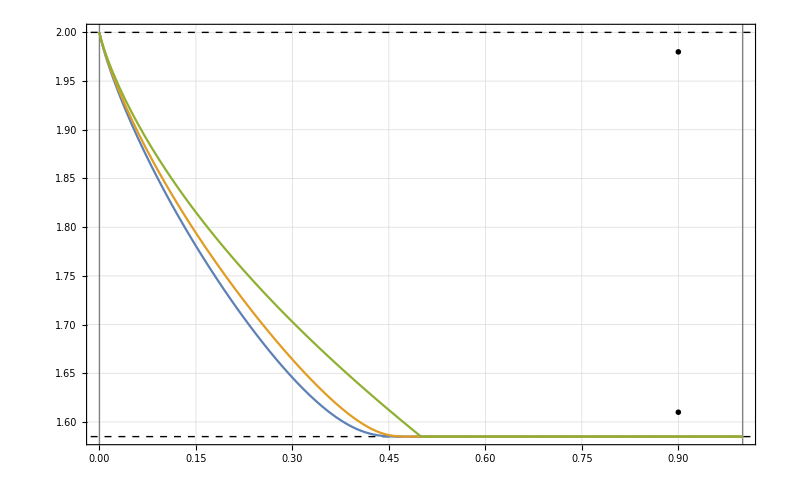

```mathematica
Show[
plot1asub1,
plot1asub2,
FrameLabel->{
MaTeX["\\gamma_{10}",Magnification->1.5],
MaTeX["Q",Magnification->1.5]
},
RotateLabel->False,
Frame->{{True,True},{True,True}},
AxesOrigin->{0,2},
PlotRange->All,
GridLines->Automatic,
Prolog->{
{
Directive[Thin,Gray],
Line[{{1,Log2[3]-0.1},{1,2.1}}],
Line[{{0,Log2[3]-0.1},{0,2.1}}]
},
{
Directive[Dashed,Thin,Black],
Line[{{-0.1,2},{1.1,2}}],
Line[{{-0.1,Log2[3]},{1.1,Log2[3]}}]
},
{
Directive[Dashed,Thin,Black],
Text[MaTeX["\\color{black} 2",Magnification->1.4],{0.9,1.98}],
Text[MaTeX["\\color{black} \\log _2 3",Magnification->1.4],{0.9,1.61}]
}
},
BaseStyle->texStyle
]
```

#### (2A) γ21=0

Set transition probabilities

```mathematica
γ//ClearAmplitudes
γ21=0;
γ30=0;
γ31=0;
γ32=0;
```

Define coherent information functions

```mathematica
ic2a[γ10_,γ20_,θ0_,θ1_,θ2_]=InfoC[ρDt,Kraus[KrausList[GammaMat[γ]]]]//Simplify;
icc2a[γ10_,γ20_]:=NMaximize[ic2a[γ10,γ20,θ0,θ1,θ2],{θ0,θ1,θ2}][[1]];
```

Plot separately

```mathematica
plot2asub1=DensityPlot[icc2a[γ10,γ20],{γ10,0,1/2},{γ20,0,1/2},ColorFunction->ColorData[{"StarryNightColors",{1,2}}],ColorFunctionScaling->False];
```

```mathematica
plot2asub2=DensityPlot[iccadc3[γ10],{γ10,0,1/2},{γ20,1/2,1},ColorFunction->ColorData[{"StarryNightColors",{1,2}}],ColorFunctionScaling->False];
```

```mathematica
plot2asub3=DensityPlot[iccadc3[γ20],{γ10,1/2,1},{γ20,0,1/2},ColorFunction->ColorData[{"StarryNightColors",{1,2}}],ColorFunctionScaling->False];
```

```mathematica
plot2asub4=DensityPlot[1,{γ10,1/2,1},{γ20,1/2,1},ColorFunction->ColorData[{"StarryNightColors",{1,2}}],ColorFunctionScaling->False];
```

```mathematica
Legended[
Show[
plot2asub1,
plot2asub2,
plot2asub3,
plot2asub4,
FrameLabel->{
MaTeX["\\gamma _{10}",Magnification->1.7],
MaTeX["\\gamma _{20}",Magnification->1.7]
},
RotateLabel->False,
Frame->{{True,True},{True,True}},
PlotRange->All,
GridLines->None,
Epilog->{
{
Directive[Thick,Red,Dashed],
Line[{Scaled[{0.5,0}],Scaled[{0.5,1}]}],
Line[{Scaled[{0,0.5}],Scaled[{1,0.5}]}]
},
{
Text[MaTeX["\\color{white}\\max _\\rho I_c \\left( \\rho ,\\Phi _{\\Gamma _{\\mathrm{2A}}(\\gamma _{10},\\gamma _{20})}\\right)",Magnification->1.7],{0.25,0.25}],
Text[MaTeX["\\color{white} 1",Magnification->1.7],{0.75,0.75}],
Text[MaTeX["\\color{white} Q\\left(\\Phi ^{(3)} _{\\Gamma _{\\mathrm{1A3}}(\\gamma _{20})}\\right)",Magnification->1.7],{0.75,0.25}],
Text[MaTeX["\\color{white} Q\\left(\\Phi ^{(3)} _{\\Gamma _{\\mathrm{1A3}}(\\gamma _{10})}\\right)",Magnification->1.7],{0.25,0.75}],
}
},
PlotLegends->Automatic,
BaseStyle->texStyle
],
BarLegend[
{"StarryNightColors",{1,2}},
LegendLabel->Placed[MaTeX["Q\\left(\\Phi _{\\Gamma _{\\mathrm{2A}}(\\gamma _{10},\\gamma _{20})}\\right)",Magnification->1.7],Right]
]
]
```

-Graphics-

Difference at border of deg region

```mathematica
plot2a2=Plot[
icc2a[γ10,1/2]-iccadc3[γ10],
{γ10,0,1/2}
];
```

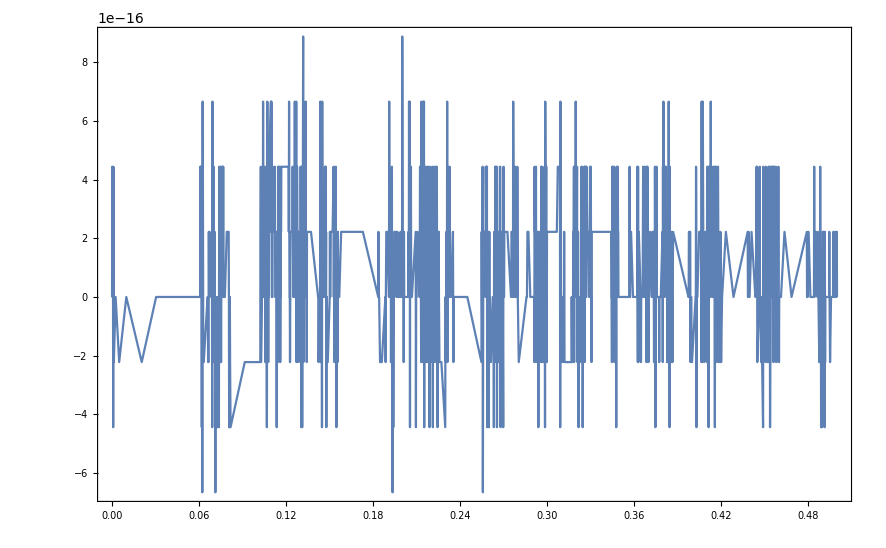

```mathematica
Show[
plot2a2,
Frame->{{True,True},{True,True}},
FrameLabel->{
MaTeX["\\gamma _{10}",Magnification->1.7],
MaTeX["Q\\left(\\Phi _{\\Gamma _\\mathrm{2A}(\\gamma _{10},\\gamma _{20}=1/2)}\\right)-Q\\left(\\Phi ^{(3)} _{\\Gamma _{\\mathrm{1A3}}(\\gamma _{10})}\\right)",Magnification->1.7]
},
RotateLabel->False,
BaseStyle->texStyle
]
```

#### (2B) γ10=0

Set transition probabilities

```mathematica
γ//ClearAmplitudes
γ10=0;
γ30=0;
γ31=0;
γ32=0;
```

Define coherent information functions

```mathematica
ic2b[γ21_,γ20_,θ0_,θ1_,θ2_]=InfoC[ρDt,Kraus[KrausList[GammaMat[γ]]]]//Simplify;
icc2b[γ21_,γ20_]:=NMaximize[ic2b[γ21,γ20,θ0,θ1,θ2],{θ0,θ1,θ2}][[1]];
```

Plot separately

```mathematica
plot2bsub1=DensityPlot[icc2b[γ21,γ20],{γ20,0,1/2},{γ21,0,1/2-γ20},ColorFunction->ColorData[{"StarryNightColors",{Log[3]/Log[2],2}}],ColorFunctionScaling->False];
```

```mathematica
plot2bsub2=DensityPlot[Log2[3],{γ20,0,1},{γ21,Max[1/2-γ20,0],1-γ20},ColorFunction->ColorData[{"StarryNightColors",{Log[3]/Log[2],2}}],ColorFunctionScaling->False];
```

```mathematica
Legended[
Show[
plot2bsub1,
plot2bsub2,
DensityPlot[0,{γ20,0,1},{γ21,1-γ20,1},ColorFunction->ColorData[{"GrayTones",{-1.5,0.5}}],ColorFunctionScaling->False],
FrameLabel->{
MaTeX["\\gamma _{20}",Magnification->1.7],
MaTeX["\\gamma _{21}",Magnification->1.7]
},
RotateLabel->False,
Frame->{{True,True},{True,True}},
PlotRange->All,
GridLines->None,
Epilog->{
{
Directive[Thick,Red,Dashed],
Line[{Scaled[{0.5,0}],Scaled[{0,0.5}]}]
},
{
Rotate[Text[MaTeX["\\color{white}\\max _\\rho I_c \\left( \\rho ,\\Phi _{\\Gamma _{\\mathrm{2B}}(\\gamma _{20},\\gamma _{21})}\\right)",Magnification->1.7],{0.17,0.17}],-Pi/4],
Rotate[Text[MaTeX["\\color{white} \\log _2 3",Magnification->1.7],{0.36,0.36}],-Pi/4]
}
},
PlotLegends->Automatic,
BaseStyle->texStyle
],
BarLegend[
{"StarryNightColors",{Log[3]/Log[2],2}},
LegendLabel->Placed[MaTeX["Q\\left(\\Phi _{\\Gamma _{\\mathrm{2B}}(\\gamma _{20},\\gamma _{21})}\\right)",Magnification->1.7],Right]
]
]
```

-Graphics-

Difference at border of deg region

```mathematica
plot2b2=Plot[
icc2b[γ21,1/2-γ21]-Log2[3],
{γ21,0,1/2}
];
```

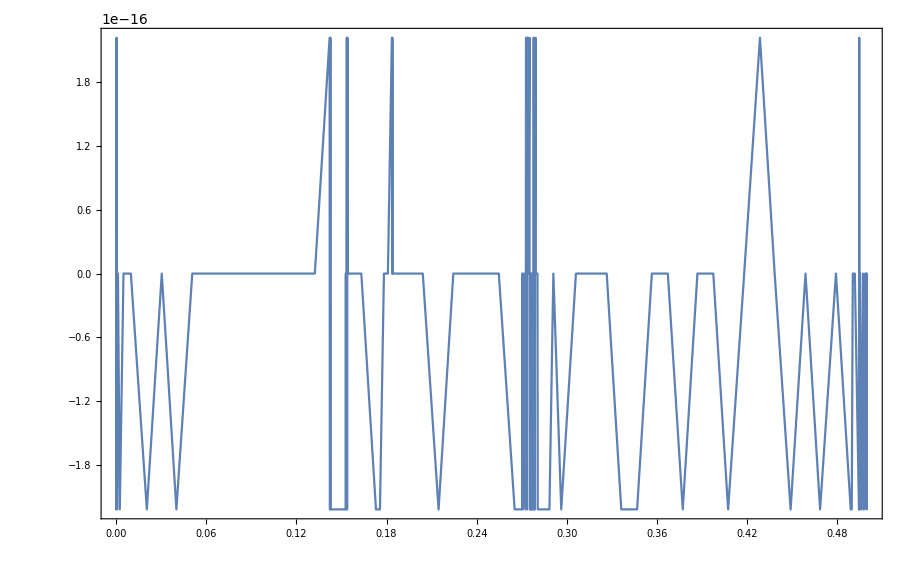

```mathematica
Show[
plot2b2,
Frame->{{True,True},{True,True}},
FrameLabel->{
MaTeX["\\gamma _{20}",Magnification->1.7],
MaTeX["Q\\left(\\Phi _{\\Gamma _\\mathrm{2B}(\\gamma _{20},1/2-\\gamma _{20})}\\right)-\\log _2 3",Magnification->1.7]
},
RotateLabel->False,
BaseStyle->texStyle
]
```

#### (2C)

Only lower bound on qcapacity

Set transition probabilities

```mathematica
γ//ClearAmplitudes
γ20=0;
γ30=0;
γ31=0;
γ32=0;
```

Define coherent information functions

```mathematica
ic2c[γ10_,γ21_,θ0_,θ1_,θ2_]=InfoC[ρDt,Kraus[KrausList[GammaMat[γ]]]];
icc2c[γ10_,γ21_]:=NMaximize[ic2c[γ10,γ21,θ0,θ1,θ2],{θ0,θ1,θ2}][[1]];
```

```mathematica
ic22c[γ10_,γ21_,θ0_,θ1_,θ2_]:=(s[Cos[θ0]^2+γ10 Cos[θ1]^2 Sin[θ0]^2]-s[γ10 Cos[θ1]^2 Sin[θ0]^2]-s[γ21 Cos[θ2]^2 Sin[θ0]^2 Sin[θ1]^2]-s[Cos[θ0]^2-1/2 Sin[θ0]^2 (2 (-1+γ10) Cos[θ1]^2+(-2+γ21+γ21 Cos[2 θ2]) Sin[θ1]^2)]+s[Sin[θ0]^2 (-((-1+γ10) Cos[θ1]^2)+γ21 Cos[θ2]^2 Sin[θ1]^2)]+s[-((-1+γ21) Cos[θ2]^2 Sin[θ0]^2 Sin[θ1]^2)]+s[Sin[θ0]^2 Sin[θ1]^2 Sin[θ2]^2])/Log[2]
```

```mathematica
icc22c[γ10_,γ21_]:=NMaximize[ic22c[γ10,γ21,θ0,θ1,θ2],{θ0,θ1,θ2},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->160][[1]];
```

```mathematica
icc22c1[γ10_,γ21_]:=NMaximize[ic22c[γ10,γ21,θ0,θ1,θ2],{θ0,θ1,θ2},WorkingPrecision->10][[1]];
```

Plot separately

```mathematica
plot2csub2=DensityPlot[icc22c[γ10,γ21],{γ10,1/2,1},{γ21,0,1},ColorFunction->ColorData[{"StarryNightColors",{1,2}}],ColorFunctionScaling->False];
```

```mathematica
plot2csub1=DensityPlot[icc22c[γ10,γ21],{γ10,0,1/2},{γ21,0,1/2},ColorFunction->ColorData[{"StarryNightColors",{1,2}}],ColorFunctionScaling->False];
```

```mathematica
plot2csub3=DensityPlot[icc22c[γ10,γ21],{γ10,0,1/2},{γ21,1/2,Max[0.5,0.4+γ10]},ColorFunction->ColorData[{"StarryNightColors",{1,2}}],ColorFunctionScaling->False];
```

```mathematica
plot2csub5=DensityPlot[icc22c1[γ10,γ21],{γ10,0,1/2},{γ21,Max[0.5,0.4+γ10],1},ColorFunction->ColorData[{"StarryNightColors",{1,2}}],ColorFunctionScaling->False];
```

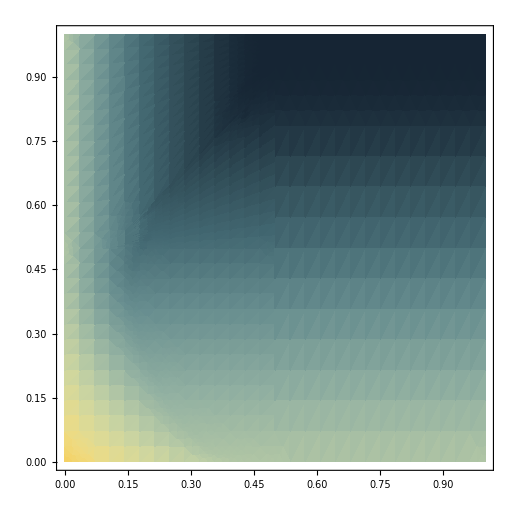

```mathematica
Legended[
Show[
plot2csub1,
plot2csub2,
plot2csub3,
plot2csub5,
FrameLabel->{
MaTeX["\\gamma _{10}",Magnification->1.7],
MaTeX["\\gamma _{21}",Magnification->1.7]
},
RotateLabel->False,
Frame->{{True,True},{True,True}},
PlotRange->All,
GridLines->None,
PlotLegends->Automatic,
BaseStyle->texStyle
],
BarLegend[
{"StarryNightColors",{Log[3]/Log[2],2}},
LegendLabel->Placed[MaTeX["\\max_{\\rho ^{(diag)}}I_c\\left(\\rho ^{(diag)},\\Phi _{\\Gamma _{\\mathrm{2C}}(\\gamma _{10},\\gamma _{21})}\\right)",Magnification->1.7],Right]
]
]
```

### (3B)

```mathematica
γ//ClearAmplitudes
γ31=0;
γ21=0;
γ20=0;
```

```mathematica
ic3b[γ10_,γ32_,γ30_,θ0_,θ1_,θ2_]=InfoC[ρDt,Kraus[KrausList[GammaMat[γ]]]]//Simplify;
icc3b[γ10_?NumericQ,γ32_?NumericQ,γ30_?NumericQ]:=NMaximize[ic3b[γ10,γ32,γ30,θ0,θ1,θ2],{θ0,θ1,θ2}][[1]];
icc3bnoQ[γ10_,γ32_,γ30_]:=NMaximize[ic3b[γ10,γ32,γ30,θ0,θ1,θ2],{θ0,θ1,θ2}][[1]];
```

```mathematica
plot3bsub1=SliceDensityPlot3D[
icc3b[γ1,γ2,γ3],
{"XStackedPlanes",{0,0.125,0.25,0.375,1/2}},
{γ1,γ2,γ3}∈ImplicitRegion[{0<=γ1<=1/2&&0<=γ2<=1/2&&0<=γ3<=1/2&&0<=γ2+γ3<=1/2},{γ1,γ2,γ3}],
ColorFunction->ColorData[{"StarryNightColors",{1,2}}],
ColorFunctionScaling->False
];
```

$Aborted

```mathematica
Legended[
Show[
plot3bsub1,
AxesLabel->{MaTeX["\\gamma _{10}",Magnification->1.5],MaTeX["\\gamma _{32}",Magnification->1.5],MaTeX["\\gamma _{30}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,0.6},{0,0.6},{0,0.6}},
AxesOrigin->{0,0,0},
BaseStyle->texStyle,
ViewPoint->{1,2,1},
ViewVertical->{1,0,0}
],
BarLegend[
{"StarryNightColors",{1,2}},
LegendLabel->Placed[MaTeX["Q\\left(\\Phi _{\\Gamma _\\mathrm{3B}(\\gamma _{10},\\gamma _{32},\\gamma _{30})}\\right)",Magnification->1.7],Right]
]
]
```

-Graphics3D-

Difference at border γ10=1/2, γ32+γ30=1/2 between Q and lower bound 1

```mathematica
plot3bdiff=Plot[
icc3bnoQ[1/2,γ21,1/2-γ21]-1,
{γ21,0,1/2}
];
```

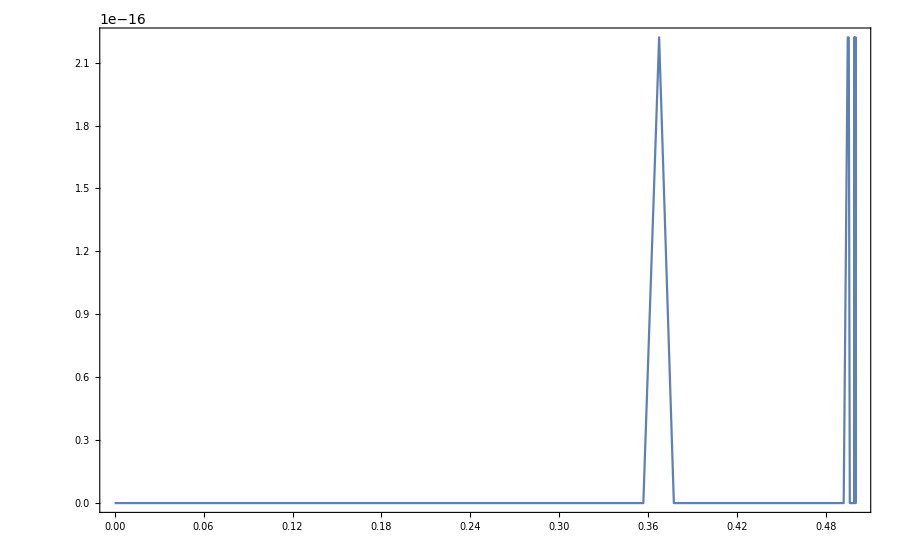

```mathematica
Show[
plot3bdiff,
Frame->{{True,True},{True,True}},
FrameLabel->{
MaTeX["\\gamma _{30}",Magnification->1.7],
MaTeX["Q\\left(\\Phi _{\\Gamma _\\mathrm{3B}(1/2,\\gamma _{30},1/2-\\gamma _{30})}\\right)-1",Magnification->1.7]
},
RotateLabel->False,
BaseStyle->texStyle
]
```

#### (2D) Indipendent ADCs

```mathematica
γ//ClearAmplitudes
γ30=0;
γ31=0;
γ21=0;
γ20=0;
```

Define coherent information functions

```mathematica
ic2d[γ10_,γ32_,θ0_,θ1_,θ2_]=InfoC[ρDt,Kraus[KrausList[GammaMat[γ]]]]//Simplify;
icc2d[γ10_,γ32_]:=NMaximize[ic2d[γ10,γ32,θ0,θ1,θ2],{θ0,θ1,θ2}][[1]];
```

Plot separately

```mathematica
plot2dsub1=DensityPlot[icc2d[γ10,γ32],{γ10,0,1/2},{γ32,0,1/2},ColorFunction->ColorData[{"StarryNightColors",{1,2}}],ColorFunctionScaling->False];
```

```mathematica
plot2dsub2=DensityPlot[iccadc3[γ10],{γ10,0,1/2},{γ32,1/2,1},ColorFunction->ColorData[{"StarryNightColors",{1,2}}],ColorFunctionScaling->False];
```

```mathematica
plot2dsub3=DensityPlot[iccadc3[γ32],{γ10,1/2,1},{γ32,0,1/2},ColorFunction->ColorData[{"StarryNightColors",{1,2}}],ColorFunctionScaling->False];
```

```mathematica
plot2dsub4=DensityPlot[1,{γ10,1/2,1},{γ32,1/2,1},ColorFunction->ColorData[{"StarryNightColors",{1,2}}],ColorFunctionScaling->False];
```

```mathematica
Legended[
Show[
plot2dsub1,
plot2dsub2,
plot2dsub3,
plot2dsub4,
FrameLabel->{
MaTeX["\\gamma _{10}",Magnification->1.7],
MaTeX["\\gamma _{32}",Magnification->1.7]
},
RotateLabel->False,
Frame->{{True,True},{True,True}},
PlotRange->All,
GridLines->None,
Epilog->{
{
Directive[Thick,Red,Dashed],
Line[{Scaled[{0.5,0}],Scaled[{0.5,1}]}],
Line[{Scaled[{0,0.5}],Scaled[{1,0.5}]}]
},
{
Text[MaTeX["\\color{white}\\max _\\rho I_c \\left( \\rho ,\\Phi _{\\Gamma _{\\mathrm{2D}}(\\gamma _{10},\\gamma _{32})}\\right)",Magnification->1.7],{0.25,0.25}],
Text[MaTeX["\\color{white} 1",Magnification->1.7],{0.75,0.75}],
Text[MaTeX["\\color{white} Q\\left(\\Phi ^{(3)} _{\\Gamma _{\\mathrm{1A3}}(\\gamma _{32})}\\right)",Magnification->1.7],{0.75,0.25}],
Text[MaTeX["\\color{white} Q\\left(\\Phi ^{(3)} _{\\Gamma _{\\mathrm{1A3}}(\\gamma _{10})}\\right)",Magnification->1.7],{0.25,0.75}],
}
},
PlotLegends->Automatic,
BaseStyle->texStyle
],
BarLegend[
{"StarryNightColors",{1,2}},
LegendLabel->Placed[MaTeX["Q\\left(\\Phi _{\\Gamma _\\mathrm{2D}(\\gamma _{10},\\gamma _{32})}\\right)",Magnification->1.7],Right]
]
]
```

-Graphics-

Numerical evaluation of the difference between the capacity and its lower bound at the edge of the degradability region

```mathematica
plot2a2=Plot[icc2d[γ10,1/2]-iccadc3[γ10],
{γ10,0,1/2}
];
```

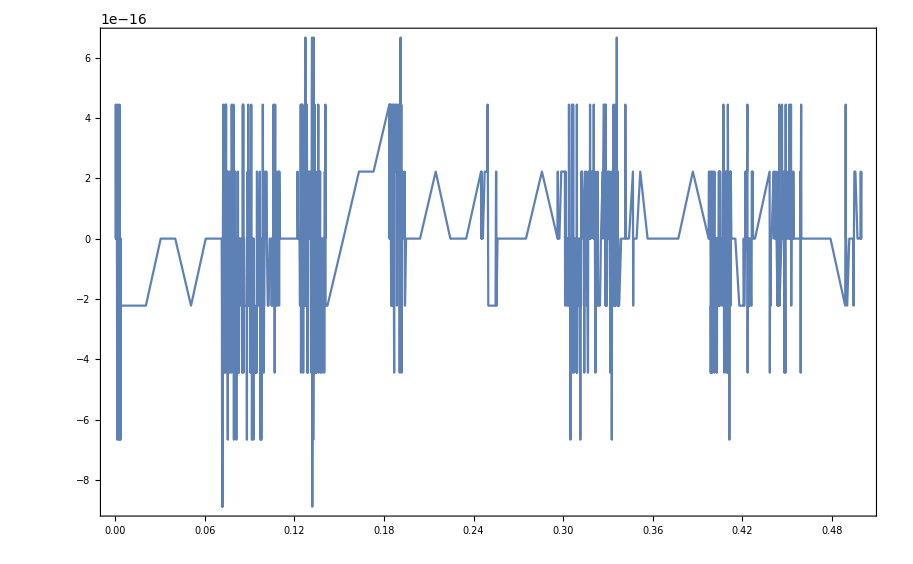

```mathematica
Show[
plot2a2,
Frame->{{True,True},{True,True}},
FrameLabel->{
MaTeX["\\gamma _{10}",Magnification->1.7],
MaTeX["Q\\left(\\Phi _{\\Gamma _\\mathrm{2D}(\\gamma _{10},\\gamma _{32}=1/2)}\\right)-Q\\left(\\Phi ^{(3)} _{\\Gamma _{\\mathrm{1A3}}(\\gamma _{10})}\\right)",Magnification->1.7]
},
RotateLabel->False,
BaseStyle->texStyle
]
```

#### Deg plots and extensions

```mathematica
existenceplot3b=RegionPlot3D[
c1[γ32,γ30]<=1&&c2[γ10]<=1,
{γ10,0,1},{γ32,0,1},{γ30,0,1},
PlotStyle->{Cyan,Opacity[0.2]},
Mesh->3,
MeshStyle->{{Gray, Opacity[0.3]},{Gray, Opacity[0.3]}},
Lighting->{"Ambient",White}
];
conditionplot3b=RegionPlot3D[
c1[γ32,γ30]<=1/2&&c2[γ10]<=1/2,
{γ10,0,1},{γ32,0,1},{γ30,0,1},
PlotStyle->{Blue,Opacity[0.5]},
Mesh->3,
MeshStyle->{{Black, Opacity[0.3]},{Black, Opacity[0.3]}},
Lighting->{"Ambient",White}
];
```

```mathematica
Show[
existenceplot3b,
conditionplot3b,
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0,0},{0.5,0,1}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0,0.5},{1,0,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,1,0},{0.5,0,0}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0.5,0},{1,0.5,0}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0.5,0},{0,0,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0.5,0},{0.5,0,0.5}}]}],
AxesLabel->{MaTeX["\\gamma _{10}",Magnification->1.5],MaTeX["\\gamma _{32}",Magnification->1.5],MaTeX["\\gamma _{30}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
GridLines->Automatic,
BaseStyle->texStyle,
FrameMargins->0.5,
ViewPoint->{0.7,1,1},
ViewVertical->{1,0,0}
]
```

-Graphics3D-

```mathematica
existenceplot2d=RegionPlot3D[c2[γ30]==0&&c2[γ32]<=1&&c2[γ10]<=1,{γ10,0,1},{γ32,0,1},{γ30,0,1},PlotStyle->{Cyan,Opacity[1]},Mesh->None,Lighting->{"Ambient",White}];
conditionplot2d=RegionPlot3D[c2[γ30]==0&&c2[γ32]<=1/2&&c2[γ10]<=1/2,{γ10,0,1},{γ32,0,1},{γ30,0,1},PlotStyle->{Blue,Opacity[1]},Mesh->None,Lighting->{"Ambient",White}];
```

```mathematica
existenceplot2a=RegionPlot3D[c2[γ32]==0&&c2[γ30]<=1&&c2[γ10]<=1,{γ10,0,1},{γ32,0,1},{γ30,0,1},PlotStyle->{Cyan,Opacity[1]},Mesh->None,Lighting->{"Ambient",White}];
conditionplot2a=RegionPlot3D[c2[γ32]==0&&c2[γ30]<=1/2&&c2[γ10]<=1/2,{γ10,0,1},{γ32,0,1},{γ30,0,1},PlotStyle->{Blue,Opacity[1]},Mesh->None,Lighting->{"Ambient",White}];
```

```mathematica
existenceplot2b=RegionPlot3D[c2[γ10]==0&&c1[γ32,γ30]<=1,{γ10,0,1},{γ32,0,1},{γ30,0,1},PlotStyle->{Cyan,Opacity[1]},Mesh->None,Lighting->{"Ambient",White}];
conditionplot2b=RegionPlot3D[c2[γ10]==0&&c1[γ32,γ30]<=1/2,{γ10,0,1},{γ32,0,1},{γ30,0,1},PlotStyle->{Blue,Opacity[1]},Mesh->None,Lighting->{"Ambient",White}];
```

```mathematica
plot22d=Show[
existenceplot2d,
conditionplot2d,
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,1,0},{0.5,0,0}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0.5,0},{1,0.5,0}}]}],
Graphics3D[Text[MaTeX["\\sim\\Phi _{\\Gamma _\\mathrm{2D}(\\gamma _{10},\\gamma _{32})}",Magnification->1.5],{0.7,0,0.7}]],
AxesLabel->{MaTeX["\\gamma _{20}",Magnification->1.5],MaTeX["\\gamma _{31}",Magnification->1.5],MaTeX["\\gamma _{30}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
GridLines->Automatic,
BaseStyle->texStyle,
FrameMargins->0.5,
ViewPoint->{0.7,1,1},
ViewVertical->{1,0,0}
]
```

-Graphics3D-

```mathematica
plot22a=Show[
conditionplot2a,
existenceplot2a,
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0,1},{0.5,0,0}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0,0.5},{1,0,0.5}}]}],
Graphics3D[Text[MaTeX["\\sim\\Phi _{\\Gamma _\\mathrm{2A}(\\gamma _{10},\\gamma _{30})}",Magnification->1.5],{0.7,0.6,0}]],
AxesLabel->{MaTeX["\\gamma _{10}",Magnification->1.5],MaTeX["\\gamma _{32}",Magnification->1.5],MaTeX["\\gamma _{30}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
GridLines->Automatic,
BaseStyle->texStyle,
FrameMargins->0.5,
ViewPoint->{0.7,1,1},
ViewVertical->{1,0,0}
]
```

-Graphics3D-

```mathematica
plot22b=Show[
existenceplot2b,
conditionplot2b,
Graphics3D[{Red,Thick,Dashed,Line[{{0,0.5,0},{0,0,0.5}}]}],
Graphics3D[Text[MaTeX["\\sim\\Phi _{\\Gamma _\\mathrm{2B}(\\gamma _{30},\\gamma _{32})}",Magnification->1.5],{0.5,0.5,0}]],
AxesLabel->{MaTeX["\\gamma _{10}",Magnification->1.5],MaTeX["\\gamma _{32}",Magnification->1.5],MaTeX["\\gamma _{30}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
GridLines->Automatic,
BaseStyle->texStyle,
FrameMargins->0.5,
ViewPoint->{0.7,1,1},
ViewVertical->{1,0,0}
]
```

-Graphics3D-

```mathematica
extensionplot3b1=RegionPlot3D[
1/2<=c1[γ32,γ30]<=1&&c2[γ10]<=1/2,
{γ10,0,1},{γ32,0,1},{γ30,0,1},
PlotStyle->{Cyan,Opacity[0.3]},
Mesh->3,
MeshStyle->{{Gray, Opacity[0.3]},{Gray, Opacity[0.3]}},
Lighting->{"Ambient",White}
];
extensionplot3b2=RegionPlot3D[
c1[γ32,γ30]<=1/2&&1/2<=c2[γ10]<=1,
{γ10,0,1},{γ32,0,1},{γ30,0,1},
PlotStyle->{Cyan,Opacity[0.3]},
Mesh->3,
MeshStyle->{{Gray, Opacity[0.3]},{Gray, Opacity[0.3]}},
Lighting->{"Ambient",White}
];
```

```mathematica
surface3bextension11=Graphics3D[
{Blue,Opacity[0.7],Polygon[{{0,1/2,0},{0,0,1/2},{1/2,0,1/2},{1/2,1/2,0}}],Lighting->{"Ambient",White}}
];
surface3bextension12=Graphics3D[
{Cyan,Opacity[0.5],Polygon[{{0,1,0},{0,0,1},{1/2,0,1},{1/2,1,0}}],Lighting->{"Ambient",White}}
];
surface3bextension21=Graphics3D[
{Blue,Opacity[0.7],Polygon[{{1/2,1/2,0},{1/2,0,1/2},{1/2,0,0}}],Lighting->{"Ambient",White}}
];
surface3bextension22=Graphics3D[
{Cyan,Opacity[0.5],Polygon[{{1,1/2,0},{1,0,1/2},{1,0,0}}],Lighting->{"Ambient",White}}
];
```

```mathematica
plot21extension1=Show[
conditionplot3b,
extensionplot3b1,
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0,0},{0.5,0,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0,0.5},{0.5,0,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0.5,0},{0.5,0,0}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0.5,0},{0.5,0.5,0}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0.5,0},{0,0,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0.5,0},{0.5,0,0.5}}]}],
AxesLabel->{MaTeX["\\gamma _{10}",Magnification->1.5],MaTeX["\\gamma _{32}",Magnification->1.5],MaTeX["\\gamma _{30}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
GridLines->Automatic,
BaseStyle->texStyle,
FrameMargins->0.5,
ViewPoint->{2,1,1},
ViewVertical->{1,0,0}
]
```

-Graphics3D-

```mathematica
plot21extension2=Show[
conditionplot3b,
extensionplot3b2,
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0,0},{0.5,0,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0,0.5},{0.5,0,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0.5,0},{0.5,0,0}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0.5,0},{0.5,0.5,0}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0.5,0},{0,0,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0.5,0},{0.5,0,0.5}}]}],
AxesLabel->{MaTeX["\\gamma _{10}",Magnification->1.5],MaTeX["\\gamma _{32}",Magnification->1.5],MaTeX["\\gamma _{30}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
GridLines->Automatic,
BaseStyle->texStyle,
FrameMargins->0.5,
ViewPoint->{1,1,1},
ViewVertical->{1,0,0}
]
```

-Graphics3D-

```mathematica
plot21extension1surfaces=Show[
surface3bextension11,
surface3bextension12,
Graphics3D[{Black,Thick,Dashed,Line[{{0.5,0,0},{0.5,0,1}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0,0,0},{0,0,1}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0,0,0.5},{0.5,0,0.5}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0.5,1,0},{0.5,0,0}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0,1,0},{0,0,0}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0,0.5,0},{0.5,0.5,0}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0,0.5,0},{0,0,0.5}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0.5,0.5,0},{0.5,0,0.5}}]}],
AxesLabel->{MaTeX["\\gamma _{10}",Magnification->1.5],MaTeX["\\gamma _{32}",Magnification->1.5],MaTeX["\\gamma _{30}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
GridLines->Automatic,
BaseStyle->texStyle,
ViewPoint->{1,1,1},
ViewVertical->{1,0,0},
Axes->True
]
```

-Graphics3D-

```mathematica
plot21extension1surfaces=Show[
surface3bextension21,
surface3bextension22,
Graphics3D[{Black,Thick,Dashed,Line[{{0.5,0,0},{0.5,0,0.5}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0,0,0.5},{1,0,0.5}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0.5,0.5,0},{0.5,0,0}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0,0.5,0},{1,0.5,0}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0.5,0.5,0},{0.5,0,0.5}}]}],
AxesLabel->{MaTeX["\\gamma _{10}",Magnification->1.5],MaTeX["\\gamma _{32}",Magnification->1.5],MaTeX["\\gamma _{30}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
GridLines->Automatic,
BaseStyle->texStyle,
ViewPoint->{1,1,1},
ViewVertical->{1,0,0},
Axes->True
]
```

-Graphics3D-

#### Difference between γ10=1/2 and γ10=1

```mathematica
γ//ClearAmplitudes
λ//ClearAmplitudes
θD=BuildDensity[θ];
τD=BuildDensityStandardDimDiagonal[θ,3];

γ20=0;
γ21=0;
γ31=0;
λ10=0;

γ10=1/2;
```

```mathematica
ic3Bdiff3[γ30_,γ32_,θ0_,θ1_,θ2_]=InfoC[θD,Kraus[KrausList[GammaMat[γ]]]];
icc3Bdiff3[γ30_,γ32_]:=NMaximize[ic3Bdiff3[γ30,γ32,θ0,θ1,θ2],{θ0,θ1,θ2}][[1]];

ic3Bdiff31[λ20_,λ21_,θ0_,θ1_]=InfoC[τD,Kraus[KrausList[GammaMatDim[λ,3]]]];
icc3Bdiff31[λ20_,λ21_]:= NMaximize[ic3Bdiff31[λ20,λ21,θ0,θ1],{θ0,θ1}][[1]];
```

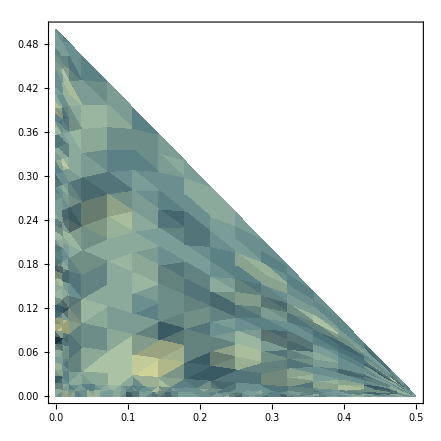

```mathematica
diff3Bplot=DensityPlot[
icc3Bdiff3[γ30,γ32]-icc3Bdiff31[γ30,γ32],
{γ30,0,1/2},{γ32,0,1/2-γ30},
FrameLabel->{
MaTeX["\\gamma _{30}",Magnification->1.7],
MaTeX["\\gamma _{32}",Magnification->1.7]
},
RotateLabel->False,
Frame->{{True,True},{True,True}},
GridLines->None,
ColorFunction->"StarryNightColors",
PlotLegends->BarLegend[
Automatic,LegendLabel->Placed[MaTeX["Q\\left(\\Phi _{\\Gamma _\\mathrm{3B}(\\gamma _{10} = 1/2,\\gamma _{30},\\gamma _{32})}\\right)-Q\\left(\\Phi^{(3)} _{\\Gamma _\\mathrm{2B3}(\\gamma _{30},\\gamma _{32})}\\right)",Magnification->1.7],Right]
]
]
```

```mathematica
γ//ClearAmplitudes
λ//ClearAmplitudes
θD=BuildDensity[θ];
τD=BuildDensityStandardDimDiagonal[θ,3];

γ20=0;
γ21=0;
γ31=0;
λ21=0;
λ20=0;
γ32=0.5-γ30;
```

```mathematica
ic3bdiff1[γ10_,γ30_,θ0_,θ1_,θ2_]=InfoC[θD,Kraus[KrausList[GammaMat[γ]]]];
icc3bdiff1[γ10_,γ30_]:=NMaximize[ic3Bdiff1[γ10,γ30,θ0,θ1,θ2],{θ0,θ1,θ2}][[1]];

ic3bdiff11[λ10_,θ0_,θ1_]=InfoC[τD,Kraus[KrausList[GammaMatDim[λ,3]]]];
icc3bdiff11[λ10_]:= NMaximize[ic3Bdiff11[λ10,θ0,θ1],{θ0,θ1}][[1]];
```

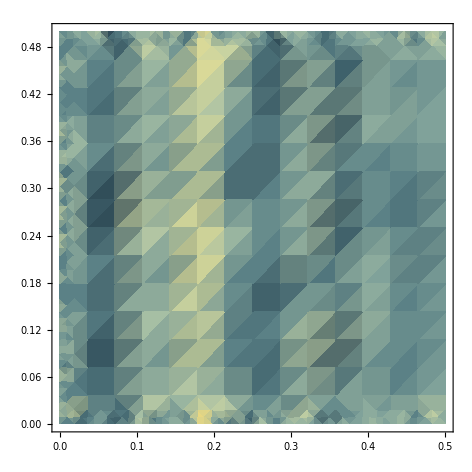

```mathematica
plot3bdiff1=DensityPlot[
icc3bdiff1[γ10,γ30]-icc3bdiff11[γ10],
{γ10,0,1/2},{γ30,0,1/2},
FrameLabel->{
MaTeX["\\gamma _{10}",Magnification->1.7],
MaTeX["\\gamma _{30}",Magnification->1.7]
},
RotateLabel->False,
Frame->{{True,True},{True,True}},
GridLines->None,
ColorFunction->"StarryNightColors",
PlotLegends->BarLegend[
Automatic,LegendLabel->Placed[MaTeX["Q\\left(\\Phi _{\\Gamma _\\mathrm{3B}(\\gamma _{10},\\gamma _{30},1/2-\\gamma _{30})}\\right)-Q\\left(\\Phi^{(3)} _{\\Gamma _\\mathrm{1A3}(\\gamma _{10})}\\right)",Magnification->1.7],Right]
]
]
```

### (3)

```mathematica
ClearAmplitudes[γ];
```

#### Setting

```mathematica
γ32=0;
γ20=0;
γ10=0;
```

### (3C)

```mathematica
ClearAmplitudes[γ];
```

```mathematica
γ31=0;
γ10=0;
γ20=0;
```

```mathematica
existenceplot3c=RegionPlot3D[
c2[γ21]<=1&&c1[γ30,γ32]<=1,
{γ21,0,1},{γ30,0,1},{γ32,0,1},
PlotStyle->{Cyan,Opacity[0.2]},
Mesh->3,
MeshStyle->{{Gray, Opacity[0.3]},{Gray, Opacity[0.3]}},
Lighting->{"Ambient",White}
];
conditionplot3c1=RegionPlot3D[
c2[γ21]==0&&c1[γ30,γ32]<=1/2,
{γ21,0,1},{γ30,0,1},{γ32,0,1},
PlotStyle->{Blue,Opacity[1]},
Mesh->None,
Lighting->{"Ambient",White}
];
conditionplot3c2=RegionPlot3D[
c2[γ21]<=1/2&&c2[γ32]==0&&c2[γ30]<=1/2,
{γ21,0,1},{γ30,0,1},{γ32,0,1},
PlotStyle->{Blue,Opacity[1]},
Mesh->None,
Lighting->{"Ambient",White}
];
```

```mathematica
Show[
existenceplot3c,
conditionplot3c1,
conditionplot3c2,
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0,0},{0.5,1,0}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0.5,0},{1,0.5,0}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0.5,0},{0,0,0.5}}]}],
AxesLabel->{MaTeX["\\gamma _{21}",Magnification->1.5],MaTeX["\\gamma _{30}",Magnification->1.5],MaTeX["\\gamma _{32}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
GridLines->Automatic,
BaseStyle->texStyle,
FrameMargins->0.5,
ViewPoint->{0.7,1,1},
ViewVertical->{1,0,0}
]
```

-Graphics3D-

### (3D)

```mathematica
ClearAmplitudes[γ];
```

```mathematica
γ31=0;
γ32=0;
γ20=0;
```

```mathematica
existenceplot3d=RegionPlot3D[
c2[γ21]<=1&&c2[γ30]<=1&&c2[γ10]<=1,
{γ10,0,1},{γ21,0,1},{γ30,0,1},
PlotStyle->{Cyan,Opacity[0.2]},
Mesh->3,
MeshStyle->{{Gray, Opacity[0.3]},{Gray, Opacity[0.3]}},
Lighting->{"Ambient",White}
];
conditionplot3d1=RegionPlot3D[
c2[γ21]==0&&c2[γ10]<=1/2&&c2[γ30]<=1/2,
{γ10,0,1},{γ21,0,1},{γ30,0,1},
PlotStyle->{Blue,Opacity[1]},
Mesh->None,
Lighting->{"Ambient",White}
];
conditionplot3d2=RegionPlot3D[
c2[γ10]==0&&c2[γ21]<=1/2&&c2[γ30]<=1/2,
{γ10,0,1},{γ21,0,1},{γ30,0,1},
PlotStyle->{Blue,Opacity[1]},
Mesh->None,
Lighting->{"Ambient",White}
];
```

```mathematica
Show[
existenceplot3d,
conditionplot3d1,
conditionplot3d2,
Graphics3D[{Red,Thick,Dashed,Line[{{0,0.5,0},{0,0.5,1}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0,0.5},{0,1,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0,0},{0.5,0,1}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0,0.5},{1,0,0.5}}]}],
AxesLabel->{MaTeX["\\gamma _{10}",Magnification->1.5],MaTeX["\\gamma _{21}",Magnification->1.5],MaTeX["\\gamma _{30}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
GridLines->Automatic,
BaseStyle->texStyle,
FrameMargins->0.5,
ViewPoint->{0.8,0.8,1},
ViewVertical->{1,0,0}
]
```

-Graphics3D-

### (3E)

```mathematica
ClearAmplitudes[γ];
```

```mathematica
γ31=0;
γ32=0;
γ21=0;
```

```mathematica
ic3e[γ10_,γ20_,γ30_,θ0_,θ1_,θ2_]=InfoC[ρDt,Kraus[KrausList[GammaMat[γ]]]]//Simplify;
icc3e[γ10_?NumericQ,γ20_?NumericQ,γ30_?NumericQ]:=NMaximize[ic3e[γ10,γ20,γ30,θ0,θ1,θ2],{θ0,θ1,θ2}][[1]];
icc3enoQ[γ10_,γ20_,γ30_]:=NMaximize[ic3e[γ10,γ20,γ30,θ0,θ1,θ2],{θ0,θ1,θ2}][[1]];
```

```mathematica
plot3esub1=SliceDensityPlot3D[
icc3e[γ1,γ2,γ3],
{"XStackedPlanes",{0,0.125,0.25,0.375,1/2}},
{γ1,γ2,γ3}∈ImplicitRegion[{0<=γ1<=1/2&&0<=γ2<=1/2&&0<=γ3<=1/2},{γ1,γ2,γ3}],
ColorFunction->ColorData[{"StarryNightColors",{0,2}}],
ColorFunctionScaling->False
];
```

$Aborted

```mathematica
Legended[
Show[
plot3esub1,
AxesLabel->{MaTeX["\\gamma _{10}",Magnification->1.5],MaTeX["\\gamma _{20}",Magnification->1.5],MaTeX["\\gamma _{30}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,0.6},{0,0.6},{0,0.6}},
AxesOrigin->{0,0,0},
BaseStyle->texStyle,
ViewPoint->{1,2,1},
ViewVertical->{1,0,0}
],
BarLegend[
{"StarryNightColors",{0,2}},
LegendLabel->Placed[MaTeX["Q\\left(\\Phi _{\\Gamma _\\mathrm{3E}(\\gamma _{10},\\gamma _{20},\\gamma _{30})}\\right)",Magnification->1.7],Right]
]
]
```

-Graphics3D-

```mathematica
icc3e[1/2,1/2,1/2]
```

4.00428×10^-17

#### Deg plots and extensions

```mathematica
existenceplot3e=RegionPlot3D[
c2[γ20]<=1&&c2[γ30]<=1&&c2[γ10]<=1,
{γ10,0,1},{γ20,0,1},{γ30,0,1},
PlotStyle->{Cyan,Opacity[0.2]},
Mesh->3,
MeshStyle->{{Gray, Opacity[0.3]},{Gray, Opacity[0.3]}},
Lighting->{"Ambient",White}
];
conditionplot3e=RegionPlot3D[
c2[γ30]<=1/2&&c2[γ20]<=1/2&&c2[γ10]<=1/2,
{γ10,0,1},{γ20,0,1},{γ30,0,1},
PlotStyle->{Blue,Opacity[0.5]},
Mesh->3,
MeshStyle->{{Black, Opacity[0.3]},{Black, Opacity[0.3]}},
Lighting->{"Ambient",White}
];
```

```mathematica
Show[
existenceplot3e,
conditionplot3e,
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0,0},{0.5,0,1}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0,0.5},{1,0,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,1,0},{0.5,0,0}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0.5,0},{1,0.5,0}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0,0.5},{0,1,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0.5,0},{0,0.5,1}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0.5,0.5},{0.5,0.5,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0.5,0},{0.5,0.5,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0,0.5},{0.5,0.5,0.5}}]}],
AxesLabel->{MaTeX["\\gamma _{10}",Magnification->1.5],MaTeX["\\gamma _{20}",Magnification->1.5],MaTeX["\\gamma _{30}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
GridLines->Automatic,
BaseStyle->texStyle,
FrameMargins->0.5,
ViewPoint->{0.8,0.9,1},
ViewVertical->{1,0,0}
]
```

-Graphics3D-

```mathematica
plot3e2a1=Show[
RegionPlot3D[c2[γ30]==0&&c2[γ10]<=1&&c2[γ20]<=1,{γ10,0,1},{γ20,0,1},{γ30,0,1},PlotStyle->{Cyan,Opacity[1]},Mesh->None,Lighting->{"Ambient",White}],
RegionPlot3D[c2[γ30]==0&&c2[γ10]<=1/2&&c2[γ20]<=1/2,{γ10,0,1},{γ20,0,1},{γ30,0,1},PlotStyle->{Blue,Opacity[1]},Mesh->None,Lighting->{"Ambient",White}],
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,1,0},{0.5,0,0}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0.5,0},{1,0.5,0}}]}],
Graphics3D[Text[MaTeX["\\sim\\Phi _{\\Gamma _\\mathrm{2A}(\\gamma _{10},\\gamma _{20})}",Magnification->1.5],{0.7,0,0.7}]],
AxesLabel->{MaTeX["\\gamma _{10}",Magnification->1.5],MaTeX["\\gamma _{20}",Magnification->1.5],MaTeX["\\gamma _{30}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
GridLines->Automatic,
BaseStyle->texStyle,
FrameMargins->0.5,
ViewPoint->{0.7,1,1},
ViewVertical->{1,0,0}
]
```

-Graphics3D-

```mathematica
plot3e2a2=Show[
RegionPlot3D[c2[γ20]==0&&c2[γ10]<=1/2&&c2[γ30]<=1/2,{γ10,0,1},{γ20,0,1},{γ30,0,1},PlotStyle->{Blue,Opacity[1]},Mesh->None,Lighting->{"Ambient",White}],
RegionPlot3D[c2[γ20]==0&&c2[γ10]<=1&&c2[γ30]<=1,{γ10,0,1},{γ20,0,1},{γ30,0,1},PlotStyle->{Cyan,Opacity[1]},Mesh->None,Lighting->{"Ambient",White}],
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0,1},{0.5,0,0}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0,0.5},{1,0,0.5}}]}],
Graphics3D[Text[MaTeX["\\sim\\Phi _{\\Gamma _\\mathrm{2A}(\\gamma _{10},\\gamma _{30})}",Magnification->1.5],{0.7,0.7,0}]],
AxesLabel->{MaTeX["\\gamma _{10}",Magnification->1.5],MaTeX["\\gamma _{20}",Magnification->1.5],MaTeX["\\gamma _{30}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
GridLines->Automatic,
BaseStyle->texStyle,
FrameMargins->0.5,
ViewPoint->{0.7,1,1},
ViewVertical->{1,0,0}
]
```

-Graphics3D-

```mathematica
plot3e2a3=Show[
RegionPlot3D[c2[γ10]==0&&c2[γ20]<=1&&c2[γ30]<=1,{γ10,0,1},{γ20,0,1},{γ30,0,1},PlotStyle->{Cyan,Opacity[1]},Mesh->None,Lighting->{"Ambient",White}],
RegionPlot3D[c2[γ10]==0&&c2[γ20]<=1/2&&c2[γ30]<=1/2,{γ10,0,1},{γ20,0,1},{γ30,0,1},PlotStyle->{Blue,Opacity[1]},Mesh->None,Lighting->{"Ambient",White}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0.5,1},{0,0.5,0}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0,0.5},{0,1,0.5}}]}],
Graphics3D[Text[MaTeX["\\sim\\Phi _{\\Gamma _\\mathrm{2A}(\\gamma _{20},\\gamma _{30})}",Magnification->1.5],{0.7,0.7,0}]],
AxesLabel->{MaTeX["\\gamma _{10}",Magnification->1.5],MaTeX["\\gamma _{20}",Magnification->1.5],MaTeX["\\gamma _{30}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
GridLines->Automatic,
BaseStyle->texStyle,
FrameMargins->0.5,
ViewPoint->{0.7,1,1},
ViewVertical->{1,0,0}
]
```

-Graphics3D-

```mathematica
extensionplot3e1=RegionPlot3D[
c2[γ30]<=1/2&&c2[γ20]<=1/2&&1/2<=c2[γ10]<=1,
{γ10,0,1},{γ20,0,1},{γ30,0,1},
PlotStyle->{Cyan,Opacity[0.2]},
Mesh->3,
MeshStyle->{{Gray, Opacity[0.3]},{Gray, Opacity[0.3]}},
Lighting->{"Ambient",White}
];
extensionplot3e2=RegionPlot3D[
c2[γ30]<=1/2&&c2[γ10]<=1/2&&1/2<=c2[γ20]<=1,
{γ10,0,1},{γ20,0,1},{γ30,0,1},
PlotStyle->{Cyan,Opacity[0.2]},
Mesh->3,
MeshStyle->{{Gray, Opacity[0.3]},{Gray, Opacity[0.3]}},
Lighting->{"Ambient",White}
];
extensionplot3e3=RegionPlot3D[
c2[γ10]<=1/2&&c2[γ20]<=1/2&&1/2<=c2[γ30]<=1,
{γ10,0,1},{γ20,0,1},{γ30,0,1},
PlotStyle->{Cyan,Opacity[0.2]},
Mesh->3,
MeshStyle->{{Gray, Opacity[0.3]},{Gray, Opacity[0.3]}},
Lighting->{"Ambient",White}
];
extensionplot3e32=RegionPlot3D[
c2[γ10]<=1/2&&1/2<=c2[γ20]<=1&&1/2<=c2[γ30]<=1,
{γ10,0,1},{γ20,0,1},{γ30,0,1},
PlotStyle->{Orange,Opacity[0.2]},
Mesh->3,
MeshStyle->{{Gray, Opacity[0.3]},{Gray, Opacity[0.3]}},
Lighting->{"Ambient",White}
];
```

```mathematica
plot3eextension1=Show[
conditionplot3e,
extensionplot3e1,
Graphics3D[{Black,Thick,Dashed,Line[{{0.5,0,0},{0.5,0,0.5}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0,0,0.5},{0.5,0,0.5}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0.5,0.5,0},{0.5,0,0}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0,0.5,0},{0.5,0.5,0}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0,0,0.5},{0,0.5,0.5}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0,0.5,0},{0,0.5,0.5}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0,0.5,0.5},{0.5,0.5,0.5}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0.5,0.5,0},{0.5,0.5,0.5}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0.5,0,0.5},{0.5,0.5,0.5}}]}],
Graphics3D[Text[MaTeX["\\sim\\Phi _{\\Gamma _\\mathrm{2B3}(\\gamma _{30},\\gamma _{20})}",Magnification->1.5],{0.9,0.9,0}]],
AxesLabel->{MaTeX["\\gamma _{10}",Magnification->1.5],MaTeX["\\gamma _{20}",Magnification->1.5],MaTeX["\\gamma _{30}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
GridLines->Automatic,
BaseStyle->texStyle,
FrameMargins->0.5,
ViewPoint->{1,1,1},
ViewVertical->{1,0,0}
]
```

-Graphics3D-

```mathematica
plot3eextension2=Show[
conditionplot3e,
extensionplot3e2,
Graphics3D[{Black,Thick,Dashed,Line[{{0.5,0,0},{0.5,0,0.5}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0,0,0.5},{0.5,0,0.5}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0.5,0.5,0},{0.5,0,0}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0,0.5,0},{0.5,0.5,0}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0,0,0.5},{0,0.5,0.5}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0,0.5,0},{0,0.5,0.5}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0,0.5,0.5},{0.5,0.5,0.5}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0.5,0.5,0},{0.5,0.5,0.5}}]}],
Graphics3D[{Black,Thick,Dashed,Line[{{0.5,0,0.5},{0.5,0.5,0.5}}]}],
Graphics3D[Text[MaTeX["\\sim\\Phi _{\\Gamma _\\mathrm{2B3}(\\gamma _{10},\\gamma _{30})}",Magnification->1.5],{0.8,0.9,0}]],
AxesLabel->{MaTeX["\\gamma _{10}",Magnification->1.5],MaTeX["\\gamma _{20}",Magnification->1.5],MaTeX["\\gamma _{30}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
GridLines->Automatic,
BaseStyle->texStyle,
FrameMargins->0.5,
ViewPoint->{1,1,1},
ViewVertical->{1,0,0}
]
```

-Graphics3D-

```mathematica
plot3eextension3=Show[
conditionplot3e,
extensionplot3e3,
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0,0},{0.5,0,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0,0.5},{0.5,0,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0.5,0},{0.5,0,0}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0.5,0},{0.5,0.5,0}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0,0.5},{0,0.5,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0.5,0},{0,0.5,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0.5,0.5},{0.5,0.5,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0.5,0},{0.5,0.5,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0,0.5},{0.5,0.5,0.5}}]}],
Graphics3D[Text[MaTeX["\\sim\\Phi _{\\Gamma _\\mathrm{2A3}(\\gamma _{10},\\gamma _{20})}",Magnification->1.5],{0.8,0,0.9}]],
AxesLabel->{MaTeX["\\gamma _{10}",Magnification->1.5],MaTeX["\\gamma _{20}",Magnification->1.5],MaTeX["\\gamma _{30}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
GridLines->Automatic,
BaseStyle->texStyle,
FrameMargins->0.5,
ViewPoint->{1,1,1},
ViewVertical->{1,0,0}
]
```

-Graphics3D-

```mathematica
plot3eextension32=Show[
conditionplot3e,
extensionplot3e3,
extensionplot3e32,
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0,0},{0.5,0,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0,0.5},{0.5,0,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0.5,0},{0.5,0,0}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0.5,0},{0.5,0.5,0}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0,0.5},{0,0.5,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0.5,0},{0,0.5,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0.5,0.5},{0.5,0.5,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0.5,0},{0.5,0.5,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0,0.5},{0.5,0.5,0.5}}]}],
Graphics3D[Text[MaTeX["\\sim ADC _{\\gamma _{10}}",Magnification->1.5],{0,0.8,0.2}]],
AxesLabel->{MaTeX["\\gamma _{10}",Magnification->1.5],MaTeX["\\gamma _{20}",Magnification->1.5],MaTeX["\\gamma _{30}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
GridLines->Automatic,
BaseStyle->texStyle,
FrameMargins->0.5,
ViewPoint->{1,1,0.2},
ViewVertical->{1,0,0}
]
```

-Graphics3D-

#### Extreme case

```mathematica
γ10=1/2;
γ20=1/2;
γ30=1/2;

ρDt=BuildDensity[θ];
NMaximize[Simplify[InfoC[ρDt,Γ]],{θ0,θ1,θ2}][[1]]//Simplify

γ10//Clear
γ20//Clear
γ30//Clear
```

0

#### Difference plots

```mathematica
γ//ClearAmplitudes
λ//ClearAmplitudes
θD=BuildDensity[θ];
τD=BuildDensityStandardDimDiagonal[θ,3];

γ21=0;
γ32=0;
γ31=0;
λ21=0;
γ30=1/2;
```

```mathematica
ic3ediff1[γ10_,γ20_,θ0_,θ1_,θ2_]=InfoC[θD,Kraus[KrausList[GammaMat[γ]]]];
icc3ediff1[γ10_,γ20_]:=NMaximize[ic3ediff1[γ10,γ20,θ0,θ1,θ2],{θ0,θ1,θ2}][[1]];

ic3ediff11[λ10_,λ20_,θ0_,θ1_]=InfoC[τD,Kraus[KrausList[GammaMatDim[λ,3]]]];
icc3ediff11[λ10_,λ20_]:= NMaximize[ic3ediff11[λ10,λ20,θ0,θ1],{θ0,θ1}][[1]];
```

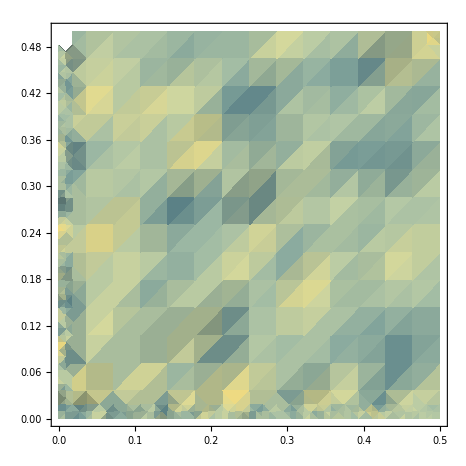

```mathematica
plot3ediff1=DensityPlot[
icc3ediff1[γ10,γ20]-icc3ediff11[γ10,γ20],
{γ10,0,1/2},{γ20,0,1/2},
FrameLabel->{
MaTeX["\\gamma _{10}",Magnification->1.7],
MaTeX["\\gamma _{20}",Magnification->1.7]
},
RotateLabel->False,
Frame->{{True,True},{True,True}},
GridLines->None,
ColorFunction->"StarryNightColors",
PlotLegends->BarLegend[
Automatic,LegendLabel->Placed[MaTeX["Q\\left(\\Phi _{\\Gamma _\\mathrm{3E}(\\gamma _{10},\\gamma _{20},1/2)}\\right)-Q\\left(\\Phi^{(3)} _{\\Gamma _\\mathrm{2A3}(\\gamma _{10},\\gamma _{20})}\\right)",Magnification->1.7],Right]
]
]
```

```mathematica
γ//ClearAmplitudes
λ//ClearAmplitudes
θD=BuildDensityStandardDimDiagonal[θ,3];
τD=BuildDensityStandardDimDiagonal[θ,2];

γ21=0;
γ20=1/2;
```

```mathematica
ic3ediff2[γ10_,θ0_,θ1_,θ2_]=InfoC[θD,Kraus[KrausList[GammaMatDim[γ,3]]]];
icc3ediff2[γ10_]:=NMaximize[ic3ediff2[γ10,θ0,θ1,θ2],{θ0,θ1,θ2}][[1]];

ic3ediff21[λ10_,θ0_]=InfoC[τD,Kraus[KrausList[GammaMatDim[λ,2]]]];
icc3ediff21[λ10_]:= NMaximize[ic3ediff21[λ10,θ0],{θ0}][[1]];
```

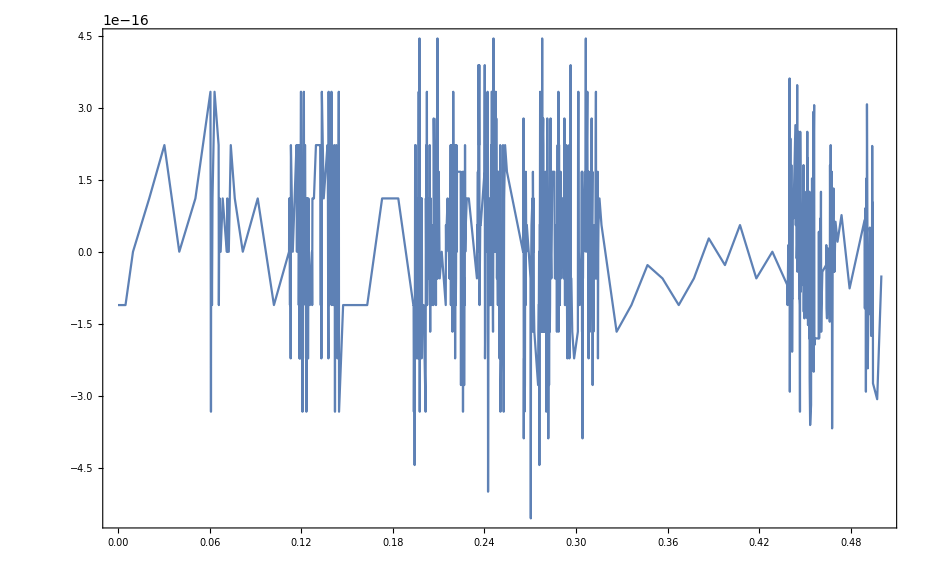

```mathematica
plot3ediff2=Plot[
icc3ediff2[γ10]-icc3ediff21[γ10],
{γ10,0,1/2},
Frame->{{True,True},{True,True}},
FrameLabel->{
MaTeX["\\gamma _{10}",Magnification->1.7],
MaTeX["Q\\left(\\Phi^{(3)} _{\\Gamma _\\mathrm{2A3}(\\gamma _{10},1/2)}\\right)-Q\\left(ADC _{\\gamma _{10}}\\right)",Magnification->1.7]
},
RotateLabel->False,
GridLines->None
]
```

### (3F)

```mathematica
ClearAmplitudes[γ];
```

```mathematica
γ21=0;
γ20=0;
γ10=0;
```

```mathematica
ic3f[γ30_,γ31_,γ32_,θ0_,θ1_,θ2_]=InfoC[ρDt,Kraus[KrausList[GammaMat[γ]]]]//Simplify;
icc3f[γ30_?NumericQ,γ31_?NumericQ,γ32_?NumericQ]:=NMaximize[ic3f[γ30,γ31,γ32,θ0,θ1,θ2],{θ0,θ1,θ2}][[1]];
icc3fnoQ[γ30_,γ31_,γ32_]:=NMaximize[ic3f[γ30,γ31,γ32,θ0,θ1,θ2],{θ0,θ1,θ2}][[1]];
```

```mathematica
plot3fsub1=SliceDensityPlot3D[
icc3f[γ1,γ2,γ3],
{"XStackedPlanes",{0,0.125,0.25,0.375,1/2}},
{γ1,γ2,γ3}∈ImplicitRegion[{0<=γ1<=1/2&&0<=γ2<=1/2&&0<=γ3<=1/2&&0<=γ1+γ2+γ3<=1/2},{γ1,γ2,γ3}],
ColorFunction->ColorData[{"StarryNightColors",{Log2[3],2}}],
ColorFunctionScaling->False
];
```

```mathematica
Legended[
Show[
plot3fsub1,
AxesLabel->{MaTeX["\\gamma _{30}",Magnification->1.5],MaTeX["\\gamma _{31}",Magnification->1.5],MaTeX["\\gamma _{32}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,0.6},{0,0.6},{0,0.6}},
AxesOrigin->{0,0,0},
BaseStyle->texStyle,
ViewPoint->{0.8,2,1},
ViewVertical->{1,0,0}
],
BarLegend[
{"StarryNightColors",{Log2[3],2}},
LegendLabel->Placed[MaTeX["Q\\left(\\Phi _{\\Gamma _\\mathrm{3F}(\\gamma _{30},\\gamma _{31},\\gamma _{32})}\\right)",Magnification->1.7],Right]
]
]
```

-Graphics3D-

#### Deg plots and extensions

```mathematica
γ32=1-γ30-γ31;
```

```mathematica
ic3fdiff[γ30_,γ31_,θ0_,θ1_,θ2_]=InfoC[ρDt,Kraus[KrausList[GammaMat[γ]]]]//Simplify;
```

```mathematica
icc3fnoQdiff[γ30_,γ31_]:=NMaximize[ic3fdiff[γ30,γ31,θ0,θ1,θ2],{θ0,θ1,θ2}][[1]];
```

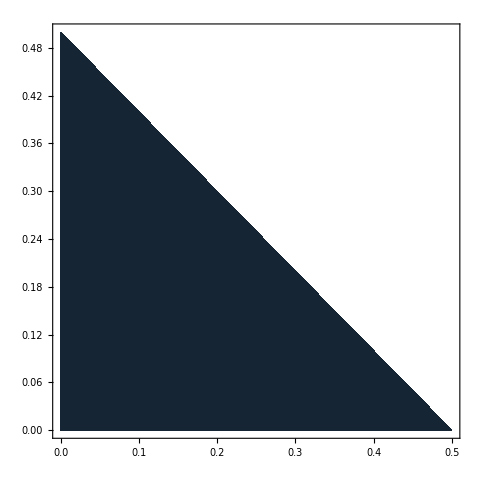

```mathematica
plot3fdiff1=DensityPlot[
icc3fnoQdiff[γ30,γ31]-Log2[3],
{γ30,0,1/2},{γ31,0,1/2-γ30},
FrameLabel->{
MaTeX["\\gamma _{30}",Magnification->1.7],
MaTeX["\\gamma _{31}",Magnification->1.7]
},
RotateLabel->False,
Frame->{{True,True},{True,True}},
GridLines->None,
ColorFunction->"StarryNightColors",
PlotLegends->BarLegend[
Automatic,LegendLabel->Placed[MaTeX["Q\\left(\\Phi _{\\Gamma _\\mathrm{3F}(\\gamma _{30},\\gamma _{31},1/2-\\gamma_{30}-\\gamma_{31})}\\right)-\\log _2 3",Magnification->1.7],Right]
]
]
```

```mathematica
existenceplot3f=RegionPlot3D[
γ30+γ31+γ32<=1,
{γ30,0,1},{γ31,0,1},{γ32,0,1},
PlotStyle->{Cyan,Opacity[0.2]},
Mesh->3,
MeshStyle->{{Gray, Opacity[0.3]},{Gray, Opacity[0.3]}},
Lighting->{"Ambient",White}
];
conditionplot3f=RegionPlot3D[
γ30+γ31+γ32<=1/2,
{γ30,0,1},{γ31,0,1},{γ32,0,1},
PlotStyle->{Blue,Opacity[0.5]},
Mesh->3,
MeshStyle->{{Black, Opacity[0.3]},{Black, Opacity[0.3]}},
Lighting->{"Ambient",White}
];
```

```mathematica
Show[
existenceplot3f,
conditionplot3f,
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0,0},{0,0.5,0}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0,0},{0,0,0.5}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0,0.5},{0,0.5,0}}]}],
AxesLabel->{MaTeX["\\gamma _{30}",Magnification->1.5],MaTeX["\\gamma _{31}",Magnification->1.5],MaTeX["\\gamma _{32}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
GridLines->Automatic,
BaseStyle->texStyle,
FrameMargins->0.5,
ViewPoint->{1,1,1},
ViewVertical->{1,0,0}
]
```

-Graphics3D-

```mathematica
plot3f2b1=Show[
RegionPlot3D[c2[γ30]==0&&c1[γ31,γ32]<=1,{γ30,0,1},{γ31,0,1},{γ32,0,1},PlotStyle->{Cyan,Opacity[1]},Mesh->None,Lighting->{"Ambient",White}],
RegionPlot3D[c2[γ30]==0&&c1[γ31,γ32]<=1/2,{γ30,0,1},{γ31,0,1},{γ32,0,1},PlotStyle->{Blue,Opacity[1]},Mesh->None,Lighting->{"Ambient",White}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0.5,0},{0,0,0.5}}]}],
Graphics3D[Text[MaTeX["\\sim\\Phi _{\\Gamma _\\mathrm{2B}(\\gamma _{31},\\gamma _{32})}",Magnification->1.5],{0.5,0,0.7}]],
AxesLabel->{MaTeX["\\gamma _{30}",Magnification->1.5],MaTeX["\\gamma _{31}",Magnification->1.5],MaTeX["\\gamma _{32}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
GridLines->Automatic,
BaseStyle->texStyle,
FrameMargins->0.5,
ViewPoint->{0.9,1,1},
ViewVertical->{1,0,0}
]
```

-Graphics3D-

```mathematica
plot3f2b2=Show[
RegionPlot3D[c2[γ31]==0&&c1[γ30,γ32]<=1/2,{γ30,0,1},{γ31,0,1},{γ32,0,1},PlotStyle->{Blue,Opacity[1]},Mesh->None,Lighting->{"Ambient",White}],
RegionPlot3D[c2[γ31]==0&&c1[γ30,γ32]<=1,{γ30,0,1},{γ31,0,1},{γ32,0,1},PlotStyle->{Cyan,Opacity[1]},Mesh->None,Lighting->{"Ambient",White}],
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0,0},{0,0,0.5}}]}],
Graphics3D[Text[MaTeX["\\sim\\Phi _{\\Gamma _\\mathrm{2B}(\\gamma _{30},\\gamma _{32})}",Magnification->1.5],{0.7,0.7,0}]],
AxesLabel->{MaTeX["\\gamma _{30}",Magnification->1.5],MaTeX["\\gamma _{31}",Magnification->1.5],MaTeX["\\gamma _{32}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
GridLines->Automatic,
BaseStyle->texStyle,
FrameMargins->0.5,
ViewPoint->{0.8,1,1},
ViewVertical->{1,0,0}
]
```

-Graphics3D-

```mathematica
plot3f2b3=Show[
RegionPlot3D[c2[γ32]==0&&c1[γ30,γ31]<=1,{γ30,0,1},{γ31,0,1},{γ32,0,1},PlotStyle->{Cyan,Opacity[1]},Mesh->None,Lighting->{"Ambient",White}],
RegionPlot3D[c2[γ32]==0&&c1[γ30,γ31]<=1/2,{γ30,0,1},{γ31,0,1},{γ32,0,1},PlotStyle->{Blue,Opacity[1]},Mesh->None,Lighting->{"Ambient",White}],
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0,0},{0,0.5,0}}]}],
Graphics3D[Text[MaTeX["\\sim\\Phi _{\\Gamma _\\mathrm{2B}(\\gamma _{30},\\gamma _{31})}",Magnification->1.5],{0.7,0,0.7}]],
AxesLabel->{MaTeX["\\gamma _{30}",Magnification->1.5],MaTeX["\\gamma _{31}",Magnification->1.5],MaTeX["\\gamma _{32}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
GridLines->Automatic,
BaseStyle->texStyle,
FrameMargins->0.5,
ViewPoint->{0.8,1,1},
ViewVertical->{1,0,0}
]
```

-Graphics3D-

### (3G)

```mathematica
ClearAmplitudes[γ];
```

```mathematica
γ32=0;
γ30=0;
γ20=0;
```

```mathematica
existenceplot3g=RegionPlot3D[
c2[γ21]<=1&&c2[γ31]<=1&&c2[γ10]<=1,
{γ10,0,1},{γ21,0,1},{γ31,0,1},
PlotStyle->{Cyan,Opacity[0.2]},
Mesh->3,
MeshStyle->{{Gray, Opacity[0.3]},{Gray, Opacity[0.3]}},
Lighting->{"Ambient",White}
];
conditionplot3g=RegionPlot3D[
c2[γ10]==0&&c2[γ21]<=1/2&&c2[γ31]<=1/2,
{γ10,0,1},{γ21,0,1},{γ31,0,1},
PlotStyle->{Blue,Opacity[1]},
Mesh->None,
Lighting->{"Ambient",White}
];
```

```mathematica
Show[
existenceplot3g,
conditionplot3g,
Graphics3D[{Red,Thick,Dashed,Line[{{0,0.5,0},{0,0.5,1}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0,0.5},{0,1,0.5}}]}],
AxesLabel->{MaTeX["\\gamma _{10}",Magnification->1.5],MaTeX["\\gamma _{21}",Magnification->1.5],MaTeX["\\gamma _{31}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
GridLines->Automatic,
BaseStyle->texStyle,
FrameMargins->0.5,
ViewPoint->{0.8,0.8,1},
ViewVertical->{1,0,0}
]
```

-Graphics3D-

### (3G)

```mathematica
ClearAmplitudes[γ];
```

```mathematica
γ31=0;
γ30=0;
γ10=0;
```

```mathematica
existenceplot3h=RegionPlot3D[
c1[γ21,γ20]<=1&&c2[γ32]<=1,
{γ20,0,1},{γ21,0,1},{γ32,0,1},
PlotStyle->{Cyan,Opacity[0.2]},
Mesh->3,
MeshStyle->{{Gray, Opacity[0.3]},{Gray, Opacity[0.3]}},
Lighting->{"Ambient",White}
];
conditionplot3h=RegionPlot3D[
c2[γ32]==0&&c1[γ21,γ20]<=1/2,
{γ20,0,1},{γ21,0,1},{γ32,0,1},
PlotStyle->{Blue,Opacity[1]},
Mesh->None,
Lighting->{"Ambient",White}
];
```

```mathematica
Show[
existenceplot3h,
conditionplot3h,
Graphics3D[{Red,Thick,Dashed,Line[{{0,0.5,0},{0.5,0,0}}]}],
AxesLabel->{MaTeX["\\gamma _{20}",Magnification->1.5],MaTeX["\\gamma _{21}",Magnification->1.5],MaTeX["\\gamma _{32}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
GridLines->Automatic,
BaseStyle->texStyle,
FrameMargins->0.5,
ViewPoint->{0.8,0.8,1},
ViewVertical->{0,0,1}
]
```

-Graphics3D-

### (3I)

#### Setting

```mathematica
ClearAmplitudes[γ];
```

```mathematica
γ31=0;
γ30=0;
γ20=0;
```

```mathematica
existenceplot3i=RegionPlot3D[
c2[γ21]<=1&&c2[γ32]<=1&&c2[γ10]<=1,
{γ10,0,1},{γ21,0,1},{γ32,0,1},
PlotStyle->{Cyan,Opacity[0.2]},
Mesh->3,
MeshStyle->{{Gray, Opacity[0.3]},{Gray, Opacity[0.3]}},
Lighting->{"Ambient",White}
];
conditionplot3i=RegionPlot3D[
c2[γ21]==0&&c2[γ32]<=1/2&&c2[γ10]<=1/2,
{γ10,0,1},{γ21,0,1},{γ32,0,1},
PlotStyle->{Blue,Opacity[1]},
Mesh->None,
Lighting->{"Ambient",White}
];
```

```mathematica
Show[
existenceplot3i,
conditionplot3i,
Graphics3D[{Red,Thick,Dashed,Line[{{0.5,0,0},{0.5,0,1}}]}],
Graphics3D[{Red,Thick,Dashed,Line[{{0,0,0.5},{1,0,0.5}}]}],
AxesLabel->{MaTeX["\\gamma _{10}",Magnification->1.5],MaTeX["\\gamma _{21}",Magnification->1.5],MaTeX["\\gamma _{32}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
GridLines->Automatic,
BaseStyle->texStyle,
FrameMargins->0.5,
ViewPoint->{0.8,0.8,1},
ViewVertical->{0,0,1}
]
```

-Graphics3D-

#### Compute Mutual Information on diagonal states

```mathematica
Γ=GammaMat[γ];
ρDt=BuildDensity[θ];

Choi9=ChoiMatrix[Kraus[KrausList[Γ]]];

ArrayReshape[Choi9.Flatten[ρA],{d,d}]//MatrixForm//Simplify

Choi9//MatrixForm//Simplify

λ//ClearAmplitudes

Λ=GammaMat[λ];

λ30=0;
λ31=0;
λ20=0;

λ10=γ10;
λ21=γ32;
λ32=γ21;

Choi9prime=ChoiMatrix[Kraus[KrausList[Λ]]];
```

(ρ00+√(1-γ10) ρ11+√(1-γ21) ρ22+√(1-γ32) ρ33 | 0 | 0 | 0
γ10 Conjugate[ρ01] | √(1-γ10) (ρ00+√(1-γ10) ρ11+√(1-γ21) ρ22+√(1-γ32) ρ33) | 0 | 0
0 | γ21 Conjugate[ρ12] | √(1-γ21) (ρ00+√(1-γ10) ρ11+√(1-γ21) ρ22+√(1-γ32) ρ33) | 0
0 | 0 | γ32 Conjugate[ρ23] | √(1-γ32) (ρ00+√(1-γ10) ρ11+√(1-γ21) ρ22+√(1-γ32) ρ33))

(1 | 0 | 0 | 0 | 0 | √(1-γ10) | 0 | 0 | 0 | 0 | √(1-γ21) | 0 | 0 | 0 | 0 | √(1-γ32)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
√(1-γ10) | 0 | 0 | 0 | 0 | 1-γ10 | 0 | 0 | 0 | 0 | √((-1+γ10) (-1+γ21)) | 0 | 0 | 0 | 0 | √((-1+γ10) (-1+γ32))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | γ21 | 0 | 0 | 0 | 0 | 0 | 0
√(1-γ21) | 0 | 0 | 0 | 0 | √((-1+γ10) (-1+γ21)) | 0 | 0 | 0 | 0 | 1-γ21 | 0 | 0 | 0 | 0 | √((-1+γ21) (-1+γ32))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | γ32 | 0
√(1-γ32) | 0 | 0 | 0 | 0 | √((-1+γ10) (-1+γ32)) | 0 | 0 | 0 | 0 | √((-1+γ21) (-1+γ32)) | 0 | 0 | 0 | 0 | 1-γ32)

### (4A)

```mathematica
ClearAmplitudes[γ];
```

```mathematica
γ10=0;
γ32=0;
```

#### difference

```mathematica
γ31=1/2-γ30;
```

```mathematica
λ//ClearAmplitudes
```

```mathematica
θD=BuildDensity[θ];
τD=BuildDensityStandardDimDiagonal[θ,3];
```

```mathematica
λ10=0;
```

```mathematica
icc4adiff1//Clear
icc4adiff//Clear
```

```mathematica
γ30=1/4;
```

```mathematica
ic4adiff1[λ20_,λ21_,θ0_,θ1_]=InfoC[τD,Kraus[KrausList[GammaMatDim[λ,3]]]]//Simplify;
icc4adiff1[λ20_,λ21_]:=NMaximize[ic4adiff1[λ20,λ21,θ0,θ1],{θ0,θ1}][[1]];
```

```mathematica
ic4adiff[γ20_,γ21_,θ0_,θ1_,θ2_]=InfoC[θD,Kraus[KrausList[GammaMat[γ]]]]//Simplify;
icc4adiff[γ20_,γ21_]:=NMaximize[ic4adiff[γ20,γ21,θ0,θ1,θ2],{θ0,θ1,θ2}][[1]];
```

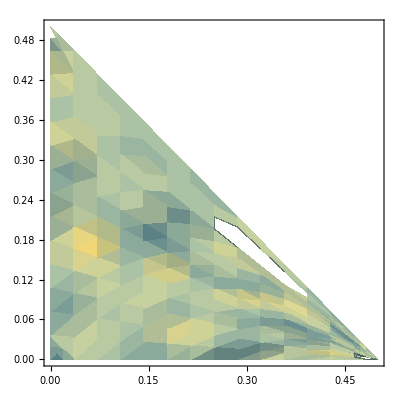

```mathematica
plot4adiff1=DensityPlot[
icc4adiff[γ20,γ21]-icc4adiff1[γ20,γ21],
{γ20,0,1/2},{γ21,0,1/2-γ20},
FrameLabel->{
MaTeX["\\gamma _{20}",Magnification->1.7],
MaTeX["\\gamma _{21}",Magnification->1.7]
},
RotateLabel->False,
Frame->{{True,True},{True,True}},
GridLines->None,
ColorFunction->"StarryNightColors",
PlotLegends->BarLegend[
Automatic,LegendLabel->Placed[MaTeX["Q\\left(\\Phi _{\\Gamma _\\mathrm{4A}(\\gamma _{20},\\gamma _{21},1/4,1/4)}\\right)-Q\\left(\\Phi _{\\Gamma _\\mathrm{2B3}(\\gamma _{20},\\gamma _{21})}\\right)",Magnification->1.7],Right]
]
]
```

```mathematica
icc4adiff1[1/2,0]
```

1.

```mathematica
icc4adiff1[0.,0.]
```

1.58496

```mathematica
maxdiff4a=0;
Do[
tmp=icc4adiff[g20,g21,g30]-icc4adiff1[g20,g21];
If[Abs[tmp]>maxdiff4a,maxdiff4a=tmp,Nothing],
{g30,0,1/2,0.04},{g20,0,1/2,0.04},{g21,0,1/2-g20,0.04}
];
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
maxdiff4a
```

2.22045×10^-16

## Coherent information for tensor product of MAD channels:

```mathematica
γ//ClearAmplitudes
λ//ClearAmplitudes

TensorProduct[MAD[γ][BuildDensityStandard[τ]],MAD[γ][BuildDensityStandard[ρ]]]//Simplify//MatrixForm
```

(((1+(-1+γ10) ρ11+(-1+γ20) ρ22+(-1+γ30) ρ33) (1+(-1+γ10) τ11+(-1+γ20) τ22+(-1+γ30) τ33) | √(1-γ10) ρ01 (1+(-1+γ10) τ11+(-1+γ20) τ22+(-1+γ30) τ33) | √(1-γ20-γ21) ρ02 (1+(-1+γ10) τ11+(-1+γ20) τ22+(-1+γ30) τ33) | √(1-γ30-γ31-γ32) ρ03 (1+(-1+γ10) τ11+(-1+γ20) τ22+(-1+γ30) τ33)
√(1-γ10) (1+(-1+γ10) τ11+(-1+γ20) τ22+(-1+γ30) τ33) Conjugate[ρ01] | (ρ11-γ10 ρ11+γ21 ρ22+γ31 ρ33) (1+(-1+γ10) τ11+(-1+γ20) τ22+(-1+γ30) τ33) | √((-1+γ10) (-1+γ20+γ21)) ρ12 (1+(-1+γ10) τ11+(-1+γ20) τ22+(-1+γ30) τ33) | √((-1+γ10) (-1+γ30+γ31+γ32)) ρ13 (1+(-1+γ10) τ11+(-1+γ20) τ22+(-1+γ30) τ33)
√(1-γ20-γ21) (1+(-1+γ10) τ11+(-1+γ20) τ22+(-1+γ30) τ33) Conjugate[ρ02] | √((-1+γ10) (-1+γ20+γ21)) (1+(-1+γ10) τ11+(-1+γ20) τ22+(-1+γ30) τ33) Conjugate[ρ12] | (-((-1+γ20+γ21) ρ22)+γ32 ρ33) (1+(-1+γ10) τ11+(-1+γ20) τ22+(-1+γ30) τ33) | √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) ρ23 (1+(-1+γ10) τ11+(-1+γ20) τ22+(-1+γ30) τ33)
√(1-γ30-γ31-γ32) (1+(-1+γ10) τ11+(-1+γ20) τ22+(-1+γ30) τ33) Conjugate[ρ03] | √((-1+γ10) (-1+γ30+γ31+γ32)) (1+(-1+γ10) τ11+(-1+γ20) τ22+(-1+γ30) τ33) Conjugate[ρ13] | √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) (1+(-1+γ10) τ11+(-1+γ20) τ22+(-1+γ30) τ33) Conjugate[ρ23] | -((-1+γ30+γ31+γ32) ρ33 (1+(-1+γ10) τ11+(-1+γ20) τ22+(-1+γ30) τ33))) | (√(1-γ10) (1+(-1+γ10) ρ11+(-1+γ20) ρ22+(-1+γ30) ρ33) τ01 | -((-1+γ10) ρ01 τ01) | √((-1+γ10) (-1+γ20+γ21)) ρ02 τ01 | √((-1+γ10) (-1+γ30+γ31+γ32)) ρ03 τ01
-((-1+γ10) τ01 Conjugate[ρ01]) | √(1-γ10) (ρ11-γ10 ρ11+γ21 ρ22+γ31 ρ33) τ01 | -((-1+γ10) √(1-γ20-γ21) ρ12 τ01) | -((-1+γ10) √(1-γ30-γ31-γ32) ρ13 τ01)
√((-1+γ10) (-1+γ20+γ21)) τ01 Conjugate[ρ02] | -((-1+γ10) √(1-γ20-γ21) τ01 Conjugate[ρ12]) | √(1-γ10) (-((-1+γ20+γ21) ρ22)+γ32 ρ33) τ01 | √(-((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32))) ρ23 τ01
√((-1+γ10) (-1+γ30+γ31+γ32)) τ01 Conjugate[ρ03] | -((-1+γ10) √(1-γ30-γ31-γ32) τ01 Conjugate[ρ13]) | √(-((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32))) τ01 Conjugate[ρ23] | -√(1-γ10) (-1+γ30+γ31+γ32) ρ33 τ01) | (√(1-γ20-γ21) (1+(-1+γ10) ρ11+(-1+γ20) ρ22+(-1+γ30) ρ33) τ02 | √((-1+γ10) (-1+γ20+γ21)) ρ01 τ02 | -((-1+γ20+γ21) ρ02 τ02) | √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) ρ03 τ02
√((-1+γ10) (-1+γ20+γ21)) τ02 Conjugate[ρ01] | √(1-γ20-γ21) (ρ11-γ10 ρ11+γ21 ρ22+γ31 ρ33) τ02 | -√(1-γ10) (-1+γ20+γ21) ρ12 τ02 | √(-((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32))) ρ13 τ02
-((-1+γ20+γ21) τ02 Conjugate[ρ02]) | -√(1-γ10) (-1+γ20+γ21) τ02 Conjugate[ρ12] | √(1-γ20-γ21) (-((-1+γ20+γ21) ρ22)+γ32 ρ33) τ02 | -((-1+γ20+γ21) √(1-γ30-γ31-γ32) ρ23 τ02)
√((-1+γ20+γ21) (-1+γ30+γ31+γ32)) τ02 Conjugate[ρ03] | √(-((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32))) τ02 Conjugate[ρ13] | -((-1+γ20+γ21) √(1-γ30-γ31-γ32) τ02 Conjugate[ρ23]) | -√(1-γ20-γ21) (-1+γ30+γ31+γ32) ρ33 τ02) | (√(1-γ30-γ31-γ32) (1+(-1+γ10) ρ11+(-1+γ20) ρ22+(-1+γ30) ρ33) τ03 | √((-1+γ10) (-1+γ30+γ31+γ32)) ρ01 τ03 | √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) ρ02 τ03 | -((-1+γ30+γ31+γ32) ρ03 τ03)
√((-1+γ10) (-1+γ30+γ31+γ32)) τ03 Conjugate[ρ01] | √(1-γ30-γ31-γ32) (ρ11-γ10 ρ11+γ21 ρ22+γ31 ρ33) τ03 | √(-((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32))) ρ12 τ03 | -√(1-γ10) (-1+γ30+γ31+γ32) ρ13 τ03
√((-1+γ20+γ21) (-1+γ30+γ31+γ32)) τ03 Conjugate[ρ02] | √(-((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32))) τ03 Conjugate[ρ12] | √(1-γ30-γ31-γ32) (-((-1+γ20+γ21) ρ22)+γ32 ρ33) τ03 | -√(1-γ20-γ21) (-1+γ30+γ31+γ32) ρ23 τ03
-((-1+γ30+γ31+γ32) τ03 Conjugate[ρ03]) | -√(1-γ10) (-1+γ30+γ31+γ32) τ03 Conjugate[ρ13] | -√(1-γ20-γ21) (-1+γ30+γ31+γ32) τ03 Conjugate[ρ23] | (1-γ30-γ31-γ32)^(3/2) ρ33 τ03)
(√(1-γ10) (1+(-1+γ10) ρ11+(-1+γ20) ρ22+(-1+γ30) ρ33) Conjugate[τ01] | -((-1+γ10) ρ01 Conjugate[τ01]) | √((-1+γ10) (-1+γ20+γ21)) ρ02 Conjugate[τ01] | √((-1+γ10) (-1+γ30+γ31+γ32)) ρ03 Conjugate[τ01]
-((-1+γ10) Conjugate[ρ01] Conjugate[τ01]) | √(1-γ10) (ρ11-γ10 ρ11+γ21 ρ22+γ31 ρ33) Conjugate[τ01] | -((-1+γ10) √(1-γ20-γ21) ρ12 Conjugate[τ01]) | -((-1+γ10) √(1-γ30-γ31-γ32) ρ13 Conjugate[τ01])
√((-1+γ10) (-1+γ20+γ21)) Conjugate[ρ02] Conjugate[τ01] | √(-(-1+γ10)^2 (-1+γ20+γ21)) Conjugate[ρ12] Conjugate[τ01] | √(1-γ10) (-((-1+γ20+γ21) ρ22)+γ32 ρ33) Conjugate[τ01] | √(-((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32))) ρ23 Conjugate[τ01]
√((-1+γ10) (-1+γ30+γ31+γ32)) Conjugate[ρ03] Conjugate[τ01] | √(-(-1+γ10)^2 (-1+γ30+γ31+γ32)) Conjugate[ρ13] Conjugate[τ01] | √(-((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32))) Conjugate[ρ23] Conjugate[τ01] | -√(1-γ10) (-1+γ30+γ31+γ32) ρ33 Conjugate[τ01]) | ((1+(-1+γ10) ρ11+(-1+γ20) ρ22+(-1+γ30) ρ33) (τ11-γ10 τ11+γ21 τ22+γ31 τ33) | √(1-γ10) ρ01 (τ11-γ10 τ11+γ21 τ22+γ31 τ33) | √(1-γ20-γ21) ρ02 (τ11-γ10 τ11+γ21 τ22+γ31 τ33) | √(1-γ30-γ31-γ32) ρ03 (τ11-γ10 τ11+γ21 τ22+γ31 τ33)
√(1-γ10) (τ11-γ10 τ11+γ21 τ22+γ31 τ33) Conjugate[ρ01] | ((-1+γ10) ρ11-γ21 ρ22-γ31 ρ33) ((-1+γ10) τ11-γ21 τ22-γ31 τ33) | √((-1+γ10) (-1+γ20+γ21)) ρ12 (τ11-γ10 τ11+γ21 τ22+γ31 τ33) | √((-1+γ10) (-1+γ30+γ31+γ32)) ρ13 (τ11-γ10 τ11+γ21 τ22+γ31 τ33)
√(1-γ20-γ21) (τ11-γ10 τ11+γ21 τ22+γ31 τ33) Conjugate[ρ02] | √((-1+γ10) (-1+γ20+γ21)) (τ11-γ10 τ11+γ21 τ22+γ31 τ33) Conjugate[ρ12] | (-((-1+γ20+γ21) ρ22)+γ32 ρ33) (τ11-γ10 τ11+γ21 τ22+γ31 τ33) | √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) ρ23 (τ11-γ10 τ11+γ21 τ22+γ31 τ33)
√(1-γ30-γ31-γ32) (τ11-γ10 τ11+γ21 τ22+γ31 τ33) Conjugate[ρ03] | √((-1+γ10) (-1+γ30+γ31+γ32)) (τ11-γ10 τ11+γ21 τ22+γ31 τ33) Conjugate[ρ13] | √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) (τ11-γ10 τ11+γ21 τ22+γ31 τ33) Conjugate[ρ23] | -((-1+γ30+γ31+γ32) ρ33 (τ11-γ10 τ11+γ21 τ22+γ31 τ33))) | (√((-1+γ10) (-1+γ20+γ21)) (1+(-1+γ10) ρ11+(-1+γ20) ρ22+(-1+γ30) ρ33) τ12 | -((-1+γ10) √(1-γ20-γ21) ρ01 τ12) | -√(1-γ10) (-1+γ20+γ21) ρ02 τ12 | √(-((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32))) ρ03 τ12
-((-1+γ10) √(1-γ20-γ21) τ12 Conjugate[ρ01]) | √((-1+γ10) (-1+γ20+γ21)) (ρ11-γ10 ρ11+γ21 ρ22+γ31 ρ33) τ12 | (-1+γ10) (-1+γ20+γ21) ρ12 τ12 | -((-1+γ10) √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) ρ13 τ12)
-√(1-γ10) (-1+γ20+γ21) τ12 Conjugate[ρ02] | (-1+γ10) (-1+γ20+γ21) τ12 Conjugate[ρ12] | -√((-1+γ10) (-1+γ20+γ21)) ((-1+γ20+γ21) ρ22-γ32 ρ33) τ12 | √((-1+γ10) (-1+γ20+γ21)^2 (-1+γ30+γ31+γ32)) ρ23 τ12
√(-((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32))) τ12 Conjugate[ρ03] | √((-1+γ10)^2 (-1+γ20+γ21) (-1+γ30+γ31+γ32)) τ12 Conjugate[ρ13] | -((-1+γ20+γ21) √((-1+γ10) (-1+γ30+γ31+γ32)) τ12 Conjugate[ρ23]) | √((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32)^2) ρ33 τ12) | (√((-1+γ10) (-1+γ30+γ31+γ32)) (1+(-1+γ10) ρ11+(-1+γ20) ρ22+(-1+γ30) ρ33) τ13 | -((-1+γ10) √(1-γ30-γ31-γ32) ρ01 τ13) | √(-((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32))) ρ02 τ13 | -√(1-γ10) (-1+γ30+γ31+γ32) ρ03 τ13
-((-1+γ10) √(1-γ30-γ31-γ32) τ13 Conjugate[ρ01]) | √((-1+γ10) (-1+γ30+γ31+γ32)) (ρ11-γ10 ρ11+γ21 ρ22+γ31 ρ33) τ13 | -((-1+γ10) √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) ρ12 τ13) | (-1+γ10) (-1+γ30+γ31+γ32) ρ13 τ13
√(-((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32))) τ13 Conjugate[ρ02] | √((-1+γ10)^2 (-1+γ20+γ21) (-1+γ30+γ31+γ32)) τ13 Conjugate[ρ12] | √((-1+γ10) (-1+γ30+γ31+γ32)) (-((-1+γ20+γ21) ρ22)+γ32 ρ33) τ13 | -√((-1+γ10) (-1+γ20+γ21)) (-1+γ30+γ31+γ32) ρ23 τ13
-√(1-γ10) (-1+γ30+γ31+γ32) τ13 Conjugate[ρ03] | (-1+γ10) (-1+γ30+γ31+γ32) τ13 Conjugate[ρ13] | √((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32)^2) τ13 Conjugate[ρ23] | -((-1+γ30+γ31+γ32) √((-1+γ10) (-1+γ30+γ31+γ32)) ρ33 τ13))
(√(1-γ20-γ21) (1+(-1+γ10) ρ11+(-1+γ20) ρ22+(-1+γ30) ρ33) Conjugate[τ02] | √((-1+γ10) (-1+γ20+γ21)) ρ01 Conjugate[τ02] | -((-1+γ20+γ21) ρ02 Conjugate[τ02]) | √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) ρ03 Conjugate[τ02]
√((-1+γ10) (-1+γ20+γ21)) Conjugate[ρ01] Conjugate[τ02] | √(1-γ20-γ21) (ρ11-γ10 ρ11+γ21 ρ22+γ31 ρ33) Conjugate[τ02] | -√(1-γ10) (-1+γ20+γ21) ρ12 Conjugate[τ02] | √(-((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32))) ρ13 Conjugate[τ02]
-((-1+γ20+γ21) Conjugate[ρ02] Conjugate[τ02]) | -√(1-γ10) (-1+γ20+γ21) Conjugate[ρ12] Conjugate[τ02] | √(1-γ20-γ21) (-((-1+γ20+γ21) ρ22)+γ32 ρ33) Conjugate[τ02] | -((-1+γ20+γ21) √(1-γ30-γ31-γ32) ρ23 Conjugate[τ02])
√((-1+γ20+γ21) (-1+γ30+γ31+γ32)) Conjugate[ρ03] Conjugate[τ02] | √(-((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32))) Conjugate[ρ13] Conjugate[τ02] | √(-(-1+γ20+γ21)^2 (-1+γ30+γ31+γ32)) Conjugate[ρ23] Conjugate[τ02] | √(-((-1+γ20+γ21) (-1+γ30+γ31+γ32)^2)) ρ33 Conjugate[τ02]) | (√((-1+γ10) (-1+γ20+γ21)) (1+(-1+γ10) ρ11+(-1+γ20) ρ22+(-1+γ30) ρ33) Conjugate[τ12] | -((-1+γ10) √(1-γ20-γ21) ρ01 Conjugate[τ12]) | -√(1-γ10) (-1+γ20+γ21) ρ02 Conjugate[τ12] | √(-((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32))) ρ03 Conjugate[τ12]
√(-(-1+γ10)^2 (-1+γ20+γ21)) Conjugate[ρ01] Conjugate[τ12] | √((-1+γ10) (-1+γ20+γ21)) (ρ11-γ10 ρ11+γ21 ρ22+γ31 ρ33) Conjugate[τ12] | (-1+γ10) (-1+γ20+γ21) ρ12 Conjugate[τ12] | √((-1+γ10)^2 (-1+γ20+γ21) (-1+γ30+γ31+γ32)) ρ13 Conjugate[τ12]
-√(1-γ10) (-1+γ20+γ21) Conjugate[ρ02] Conjugate[τ12] | (-1+γ10) (-1+γ20+γ21) Conjugate[ρ12] Conjugate[τ12] | -√((-1+γ10) (-1+γ20+γ21)) ((-1+γ20+γ21) ρ22-γ32 ρ33) Conjugate[τ12] | -((-1+γ20+γ21) √((-1+γ10) (-1+γ30+γ31+γ32)) ρ23 Conjugate[τ12])
√(-((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32))) Conjugate[ρ03] Conjugate[τ12] | -((-1+γ10) √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) Conjugate[ρ13] Conjugate[τ12]) | √((-1+γ10) (-1+γ20+γ21)^2 (-1+γ30+γ31+γ32)) Conjugate[ρ23] Conjugate[τ12] | √((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32)^2) ρ33 Conjugate[τ12]) | ((1+(-1+γ10) ρ11+(-1+γ20) ρ22+(-1+γ30) ρ33) (-((-1+γ20+γ21) τ22)+γ32 τ33) | √(1-γ10) ρ01 (-((-1+γ20+γ21) τ22)+γ32 τ33) | √(1-γ20-γ21) ρ02 (-((-1+γ20+γ21) τ22)+γ32 τ33) | √(1-γ30-γ31-γ32) ρ03 (-((-1+γ20+γ21) τ22)+γ32 τ33)
√(1-γ10) (-((-1+γ20+γ21) τ22)+γ32 τ33) Conjugate[ρ01] | (ρ11-γ10 ρ11+γ21 ρ22+γ31 ρ33) (-((-1+γ20+γ21) τ22)+γ32 τ33) | -√((-1+γ10) (-1+γ20+γ21)) ρ12 ((-1+γ20+γ21) τ22-γ32 τ33) | √((-1+γ10) (-1+γ30+γ31+γ32)) ρ13 (-((-1+γ20+γ21) τ22)+γ32 τ33)
√(1-γ20-γ21) (-((-1+γ20+γ21) τ22)+γ32 τ33) Conjugate[ρ02] | -√((-1+γ10) (-1+γ20+γ21)) ((-1+γ20+γ21) τ22-γ32 τ33) Conjugate[ρ12] | ((-1+γ20+γ21) ρ22-γ32 ρ33) ((-1+γ20+γ21) τ22-γ32 τ33) | -√((-1+γ20+γ21) (-1+γ30+γ31+γ32)) ρ23 ((-1+γ20+γ21) τ22-γ32 τ33)
√(1-γ30-γ31-γ32) (-((-1+γ20+γ21) τ22)+γ32 τ33) Conjugate[ρ03] | √((-1+γ10) (-1+γ30+γ31+γ32)) (-((-1+γ20+γ21) τ22)+γ32 τ33) Conjugate[ρ13] | -√((-1+γ20+γ21) (-1+γ30+γ31+γ32)) ((-1+γ20+γ21) τ22-γ32 τ33) Conjugate[ρ23] | (-1+γ30+γ31+γ32) ρ33 ((-1+γ20+γ21) τ22-γ32 τ33)) | (√((-1+γ20+γ21) (-1+γ30+γ31+γ32)) (1+(-1+γ10) ρ11+(-1+γ20) ρ22+(-1+γ30) ρ33) τ23 | √(-((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32))) ρ01 τ23 | -((-1+γ20+γ21) √(1-γ30-γ31-γ32) ρ02 τ23) | -√(1-γ20-γ21) (-1+γ30+γ31+γ32) ρ03 τ23
√(-((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32))) τ23 Conjugate[ρ01] | √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) (ρ11-γ10 ρ11+γ21 ρ22+γ31 ρ33) τ23 | √((-1+γ10) (-1+γ20+γ21)^2 (-1+γ30+γ31+γ32)) ρ12 τ23 | -√((-1+γ10) (-1+γ20+γ21)) (-1+γ30+γ31+γ32) ρ13 τ23
-((-1+γ20+γ21) √(1-γ30-γ31-γ32) τ23 Conjugate[ρ02]) | -((-1+γ20+γ21) √((-1+γ10) (-1+γ30+γ31+γ32)) τ23 Conjugate[ρ12]) | -√((-1+γ20+γ21) (-1+γ30+γ31+γ32)) ((-1+γ20+γ21) ρ22-γ32 ρ33) τ23 | (-1+γ20+γ21) (-1+γ30+γ31+γ32) ρ23 τ23
√(-((-1+γ20+γ21) (-1+γ30+γ31+γ32)^2)) τ23 Conjugate[ρ03] | √((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32)^2) τ23 Conjugate[ρ13] | √((-1+γ20+γ21)^2 (-1+γ30+γ31+γ32)^2) τ23 Conjugate[ρ23] | -((-1+γ30+γ31+γ32) √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) ρ33 τ23))
(√(1-γ30-γ31-γ32) (1+(-1+γ10) ρ11+(-1+γ20) ρ22+(-1+γ30) ρ33) Conjugate[τ03] | √((-1+γ10) (-1+γ30+γ31+γ32)) ρ01 Conjugate[τ03] | √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) ρ02 Conjugate[τ03] | -((-1+γ30+γ31+γ32) ρ03 Conjugate[τ03])
√((-1+γ10) (-1+γ30+γ31+γ32)) Conjugate[ρ01] Conjugate[τ03] | √(1-γ30-γ31-γ32) (ρ11-γ10 ρ11+γ21 ρ22+γ31 ρ33) Conjugate[τ03] | √(-((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32))) ρ12 Conjugate[τ03] | -√(1-γ10) (-1+γ30+γ31+γ32) ρ13 Conjugate[τ03]
√((-1+γ20+γ21) (-1+γ30+γ31+γ32)) Conjugate[ρ02] Conjugate[τ03] | √(-((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32))) Conjugate[ρ12] Conjugate[τ03] | √(1-γ30-γ31-γ32) (-((-1+γ20+γ21) ρ22)+γ32 ρ33) Conjugate[τ03] | √(-((-1+γ20+γ21) (-1+γ30+γ31+γ32)^2)) ρ23 Conjugate[τ03]
-((-1+γ30+γ31+γ32) Conjugate[ρ03] Conjugate[τ03]) | -√(1-γ10) (-1+γ30+γ31+γ32) Conjugate[ρ13] Conjugate[τ03] | -√(1-γ20-γ21) (-1+γ30+γ31+γ32) Conjugate[ρ23] Conjugate[τ03] | (1-γ30-γ31-γ32)^(3/2) ρ33 Conjugate[τ03]) | (√((-1+γ10) (-1+γ30+γ31+γ32)) (1+(-1+γ10) ρ11+(-1+γ20) ρ22+(-1+γ30) ρ33) Conjugate[τ13] | -((-1+γ10) √(1-γ30-γ31-γ32) ρ01 Conjugate[τ13]) | √(-((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32))) ρ02 Conjugate[τ13] | -√(1-γ10) (-1+γ30+γ31+γ32) ρ03 Conjugate[τ13]
√(-(-1+γ10)^2 (-1+γ30+γ31+γ32)) Conjugate[ρ01] Conjugate[τ13] | √((-1+γ10) (-1+γ30+γ31+γ32)) (ρ11-γ10 ρ11+γ21 ρ22+γ31 ρ33) Conjugate[τ13] | √((-1+γ10)^2 (-1+γ20+γ21) (-1+γ30+γ31+γ32)) ρ12 Conjugate[τ13] | (-1+γ10) (-1+γ30+γ31+γ32) ρ13 Conjugate[τ13]
√(-((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32))) Conjugate[ρ02] Conjugate[τ13] | -((-1+γ10) √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) Conjugate[ρ12] Conjugate[τ13]) | √((-1+γ10) (-1+γ30+γ31+γ32)) (-((-1+γ20+γ21) ρ22)+γ32 ρ33) Conjugate[τ13] | √((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32)^2) ρ23 Conjugate[τ13]
-√(1-γ10) (-1+γ30+γ31+γ32) Conjugate[ρ03] Conjugate[τ13] | (-1+γ10) (-1+γ30+γ31+γ32) Conjugate[ρ13] Conjugate[τ13] | -√((-1+γ10) (-1+γ20+γ21)) (-1+γ30+γ31+γ32) Conjugate[ρ23] Conjugate[τ13] | -((-1+γ30+γ31+γ32) √((-1+γ10) (-1+γ30+γ31+γ32)) ρ33 Conjugate[τ13])) | (√((-1+γ20+γ21) (-1+γ30+γ31+γ32)) (1+(-1+γ10) ρ11+(-1+γ20) ρ22+(-1+γ30) ρ33) Conjugate[τ23] | √(-((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32))) ρ01 Conjugate[τ23] | -((-1+γ20+γ21) √(1-γ30-γ31-γ32) ρ02 Conjugate[τ23]) | -√(1-γ20-γ21) (-1+γ30+γ31+γ32) ρ03 Conjugate[τ23]
√(-((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32))) Conjugate[ρ01] Conjugate[τ23] | √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) (ρ11-γ10 ρ11+γ21 ρ22+γ31 ρ33) Conjugate[τ23] | -((-1+γ20+γ21) √((-1+γ10) (-1+γ30+γ31+γ32)) ρ12 Conjugate[τ23]) | √((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32)^2) ρ13 Conjugate[τ23]
√(-(-1+γ20+γ21)^2 (-1+γ30+γ31+γ32)) Conjugate[ρ02] Conjugate[τ23] | √((-1+γ10) (-1+γ20+γ21)^2 (-1+γ30+γ31+γ32)) Conjugate[ρ12] Conjugate[τ23] | -√((-1+γ20+γ21) (-1+γ30+γ31+γ32)) ((-1+γ20+γ21) ρ22-γ32 ρ33) Conjugate[τ23] | √((-1+γ20+γ21)^2 (-1+γ30+γ31+γ32)^2) ρ23 Conjugate[τ23]
-√(1-γ20-γ21) (-1+γ30+γ31+γ32) Conjugate[ρ03] Conjugate[τ23] | -√((-1+γ10) (-1+γ20+γ21)) (-1+γ30+γ31+γ32) Conjugate[ρ13] Conjugate[τ23] | (-1+γ20+γ21) (-1+γ30+γ31+γ32) Conjugate[ρ23] Conjugate[τ23] | -((-1+γ30+γ31+γ32) √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) ρ33 Conjugate[τ23])) | (-((-1+γ30+γ31+γ32) (1+(-1+γ10) ρ11+(-1+γ20) ρ22+(-1+γ30) ρ33) τ33) | -√(1-γ10) (-1+γ30+γ31+γ32) ρ01 τ33 | -√(1-γ20-γ21) (-1+γ30+γ31+γ32) ρ02 τ33 | (1-γ30-γ31-γ32)^(3/2) ρ03 τ33
-√(1-γ10) (-1+γ30+γ31+γ32) τ33 Conjugate[ρ01] | -((-1+γ30+γ31+γ32) (ρ11-γ10 ρ11+γ21 ρ22+γ31 ρ33) τ33) | √((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32)^2) ρ12 τ33 | -((-1+γ30+γ31+γ32) √((-1+γ10) (-1+γ30+γ31+γ32)) ρ13 τ33)
√(-((-1+γ20+γ21) (-1+γ30+γ31+γ32)^2)) τ33 Conjugate[ρ02] | √((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32)^2) τ33 Conjugate[ρ12] | (-1+γ30+γ31+γ32) ((-1+γ20+γ21) ρ22-γ32 ρ33) τ33 | -((-1+γ30+γ31+γ32) √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) ρ23 τ33)
(1-γ30-γ31-γ32)^(3/2) τ33 Conjugate[ρ03] | -((-1+γ30+γ31+γ32) √((-1+γ10) (-1+γ30+γ31+γ32)) τ33 Conjugate[ρ13]) | -((-1+γ30+γ31+γ32) √((-1+γ20+γ21) (-1+γ30+γ31+γ32)) τ33 Conjugate[ρ23]) | (-1+γ30+γ31+γ32)^2 ρ33 τ33))

## Hail mary

```mathematica
CustomChoiL[mat_,matinv_]:=(
CM1=ConstantArray[0,{d*d,d*d}];
dm=ConstantArray[0,{d,d}];

Do[
dm[[ik,jk]]=1;
dm1=InverseMAD[dm,matinv];
dm2=Kraus[KrausList[mat]][dm1];
dm[[ik,jk]]=0;
Do[
CM1[[(ik-1)*d+iik,(jk-1)*d+jjk]]=Simplify[dm2[[iik,jjk]]],
{iik,1,d},{jjk,1,d}
],
{ik,1,d},{jk,1,d}
];

CM1//Simplify
);

CustomChoiR[mat_,matinv_]:=(
CM1=ConstantArray[0,{d*d,d*d}];
dm=ConstantArray[0,{d,d}];

Do[
dm[[ik,jk]]=1;
dm1=Kraus[KrausList[mat]][dm];
dm2=InverseMAD[dm1,matinv];
dm[[ik,jk]]=0;
Do[
CM1[[(ik-1)*d+iik,(jk-1)*d+jjk]]=Simplify[dm2[[iik,jjk]]],
{iik,1,d},{jjk,1,d}
],
{ik,1,d},{jk,1,d}
];

CM1//Simplify
);
```

```mathematica
gamma21monoplot=RegionPlot3D[
0<=x+y<=1&&x>=z,
{x,0,1},{y,0,1},{z,0,1},
PlotStyle->{Red,Opacity[0.7]},
PlotPoints->100,
Mesh->10,
Lighting->"Standard"
];
```

```mathematica
gamma20monoplot=RegionPlot3D[
0<=x+y<=1&&y+z<=1,
{x,0,1},{y,0,1},{z,0,1},
PlotStyle->{Orange,Opacity[0.6]},
PlotPoints->100,
Mesh->10,
Lighting->"Accent"
];
```

```mathematica
gamma20monoplotAlpha=RegionPlot3D[
0<=x+y<=1&&y+z<=1,
{x,0,1},{y,0,1},{z,0,1},
PlotStyle->{Orange,Opacity[0.2]},
PlotPoints->100,
Mesh->10,
Lighting->"Standard"
];
```

```mathematica
Show[
gamma21monoplot,
AxesLabel->{MaTeX["\\gamma _{20}",Magnification->1.5],MaTeX["\\gamma _{21}",Magnification->1.5],MaTeX["\\gamma _{10}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
BaseStyle->texStyle,
ViewPoint->{0.5,1,2},
ViewVertical->{0,1,0}
]
```

-Graphics3D-

```mathematica
Show[
gamma20monoplot,
AxesLabel->{MaTeX["\\gamma _{20}",Magnification->1.5],MaTeX["\\gamma _{21}",Magnification->1.5],MaTeX["\\gamma _{10}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
BaseStyle->texStyle,
ViewPoint->{0.5,1,2},
ViewVertical->{0,1,0}
]
```

-Graphics3D-

```mathematica
Show[
gamma20monoplotAlpha,
gamma21monoplot,
AxesLabel->{MaTeX["\\gamma _{20}",Magnification->1.5],MaTeX["\\gamma _{21}",Magnification->1.5],MaTeX["\\gamma _{10}",Magnification->1.5]},
Boxed->False,
PlotRange->{{0,1.1},{0,1.1},{0,1.1}},
AxesOrigin->{0,0,0},
BaseStyle->texStyle,
ViewPoint->{0.5,1,2},
ViewVertical->{0,1,0}
]
```

-Graphics3D-

```mathematica
γ//ClearAmplitudes
λ//ClearAmplitudes
ω//ClearAmplitudes

λ10=γ10;
λ20=γ20+ϵ20;
λ21=γ21;
λ30=γ30;
λ31=γ31;
λ32=γ32;

AddAssumption[0<ϵ<(1-γ20-γ21)];

choi1//Clear
choi1=CustomChoiR[GammaMat[λ],GammaMat[γ]]//Simplify;
choi1//Eigenvalues//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,(γ21 ϵ20)/((-1+γ10) (-1+γ20+γ21)),-((-1+γ10+γ21) ϵ20)/((-1+γ10) (-1+γ20+γ21)),(-4+4 γ20+4 γ21+ϵ20)/(-1+γ20+γ21)}